#### Fix r = k2/k1 and let k1 evolve with time.

```mathematica
K[tp_] = {{0, -λ*(T-tp)}, {-r*K1[tp], K1[tp]}}
```

{{0,-(T-tp) λ},{-r K1[tp],K1[tp]}}

```mathematica
B[tp_] = {{σg, 0}, {0, K1'[tp]*σξ}}
```

{{σg,0},{0,σξ K1'[tp]}}

```mathematica
s0 = {{x0, xx0},{xx0, xh0}}
```

{{x0,xx0},{xx0,xh0}}

#### Get the initial cost

```mathematica
FullSimplify[(MatrixExp[K[0]].s0.MatrixExp[Transpose[K[0]]])[[1,1]]]
```

1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-2 T λ (T xh0 λ+(-r x0+xx0) K1[0])+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2)-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])

#### Variation in the initial cost with K

```mathematica
varS0 =FullSimplify[D[%98, K1[0]]]
```

1/(K1[0]^2 (4 r T λ+K1[0])^(5/2))2 ⅇ^K1[0] T λ (Cosh[√K1[0] √(4 r T λ+K1[0])] √(4 r T λ+K1[0]) (-4 r T^2 xh0 λ^2+2 T λ (-xh0+2 r T (xh0-2 r xx0) λ) K1[0]+(r x0-xx0+T (xh0-2 r xx0) λ) K1[0]^2)+√(4 r T λ+K1[0]) (4 r T^2 xh0 λ^2+2 T xh0 λ (1-2 r T λ) K1[0]+(-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ) K1[0]^2+(r x0-xx0) K1[0]^3)+√K1[0] (4 r T λ+K1[0]) (2 r T λ (xx0+T xh0 λ)+(-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])

#### Write down the Lagrangian

```mathematica
L[K1[tp], K1'[tp], tp] = FullSimplify[(MatrixExp[K[tp]].B[tp].Transpose[B[tp]].MatrixExp[Transpose[K[tp]]])[[1,1]]]
```

1/(2 K1[tp] (4 r (T-tp) λ+K1[tp]))ⅇ^(K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)

#### Get the boundary term

```mathematica
b0 =FullSimplify[ ExpToTrig[D[L[K1[tp], K1'[tp], tp], K1'[tp]]/.tp->0]]
```

(4 ⅇ^K1[0] T^2 λ^2 σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1'[0])/(K1[0] (4 r T λ+K1[0]))

#### Combine the boundary term and the initial cost to get the boundary condition

```mathematica
1/(K1[0]^2 (4 r T λ+K1[0])^(5/2))2 ⅇ^K1[0] T λ (Cosh[√K1[0] √(4 r T λ+K1[0])] √(4 r T λ+K1[0]) (-4 r T^2 xh0 λ^2+2 T λ (-xh0+2 r T (xh0-2 r xx0) λ) K1[0]+(r x0-xx0+T (xh0-2 r xx0) λ) K1[0]^2)+√(4 r T λ+K1[0]) (4 r T^2 xh0 λ^2+2 T xh0 λ (1-2 r T λ) K1[0]+(-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ) K1[0]^2+(r x0-xx0) K1[0]^3)+√K1[0] (4 r T λ+K1[0]) (2 r T λ (xx0+T xh0 λ)+(-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])==(4 ⅇ^K1[0] T^2 λ^2 σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1'[0])/(K1[0] (4 r T λ+K1[0]))
```

1/(K1[0]^2 (4 r T λ+K1[0])^(5/2))2 ⅇ^K1[0] T λ (Cosh[√K1[0] √(4 r T λ+K1[0])] √(4 r T λ+K1[0]) (-4 r T^2 xh0 λ^2+2 T λ (-xh0+2 r T (xh0-2 r xx0) λ) K1[0]+(r x0-xx0+T (xh0-2 r xx0) λ) K1[0]^2)+√(4 r T λ+K1[0]) (4 r T^2 xh0 λ^2+2 T xh0 λ (1-2 r T λ) K1[0]+(-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ) K1[0]^2+(r x0-xx0) K1[0]^3)+√K1[0] (4 r T λ+K1[0]) (2 r T λ (xx0+T xh0 λ)+(-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])==(4 ⅇ^K1[0] T^2 λ^2 σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1'[0])/(K1[0] (4 r T λ+K1[0]))

```mathematica
FullSimplify[%]
```

1/(K1[0]^2 (4 r T λ+K1[0])^2)2 ⅇ^K1[0] T λ (4 r T^2 xh0 λ^2+2 T xh0 λ (1-2 r T λ) K1[0]+(-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ) K1[0]^2+(r x0-xx0) K1[0]^3-Cosh[√K1[0] √(4 r T λ+K1[0])] (4 r T^2 xh0 λ^2+2 T λ (xh0-2 r T (xh0-2 r xx0) λ) K1[0]+(-r x0+xx0-T xh0 λ+2 r T xx0 λ) K1[0]^2)+√K1[0] √(4 r T λ+K1[0]) (2 r T λ (xx0+T xh0 λ)+(-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1[0] (4 r T λ+K1[0]) K1'[0])==0

```mathematica
(4 r T^2 xh0 λ^2+2 T xh0 λ (1-2 r T λ) K1[0]+(-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ) K1[0]^2+(r x0-xx0) K1[0]^3-Cosh[√K1[0] √(4 r T λ+K1[0])] (4 r T^2 xh0 λ^2+2 T λ (xh0-2 r T (xh0-2 r xx0) λ) K1[0]+(-r x0+xx0-T xh0 λ+2 r T xx0 λ) K1[0]^2)+√K1[0] √(4 r T λ+K1[0]) (2 r T λ (xx0+T xh0 λ)+(-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1[0] (4 r T λ+K1[0]) K1'[0])==0
```

4 r T^2 xh0 λ^2+2 T xh0 λ (1-2 r T λ) K1[0]+(-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ) K1[0]^2+(r x0-xx0) K1[0]^3-Cosh[√K1[0] √(4 r T λ+K1[0])] (4 r T^2 xh0 λ^2+2 T λ (xh0-2 r T (xh0-2 r xx0) λ) K1[0]+(-r x0+xx0-T xh0 λ+2 r T xx0 λ) K1[0]^2)+√K1[0] √(4 r T λ+K1[0]) (2 r T λ (xx0+T xh0 λ)+(-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1[0] (4 r T λ+K1[0]) K1'[0]==0

#### Since K1(0) >> λT, expand in small ε

```mathematica
%103/.K1[0]->-T*λ/ep
```

4 r T^2 xh0 λ^2-(T^3 (r x0-xx0) λ^3)/ep^3-(2 T^2 xh0 λ^2 (1-2 r T λ))/ep+(T^2 λ^2 (-r x0+xx0+T (4 r^2 x0-xh0-4 r xx0) λ))/ep^2-(4 r T^2 xh0 λ^2+(T^2 λ^2 (-r x0+xx0-T xh0 λ+2 r T xx0 λ))/ep^2-(2 T^2 λ^2 (xh0-2 r T (xh0-2 r xx0) λ))/ep) Cosh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)]+√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ) (2 r T λ (xx0+T xh0 λ)-(T λ (-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ))/ep) Sinh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)]+(2 T^2 λ^2 (-(T λ)/ep+4 r T λ) σξ^2 (-1+Cosh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)]) K1'[0])/ep==0

```mathematica
FullSimplify[%104, Assumptions->{4*r*T*λ>0, ep>0, 4*ep*r<1}]
```

ep (r x0+2 ep xh0-4 ep^2 r xh0-xx0+√(1-4 ep r) (xx0-r (x0+2 ep xx0)+T (2 r^2 x0+xh0-2 r (ep xh0+xx0)) λ) Sinh[(√(1-4 ep r) T λ)/ep]+2 (-1+4 ep r) T λ σξ^2 K1'[0]+Cosh[(√(1-4 ep r) T λ)/ep] (-r x0-2 ep xh0+4 ep^2 r xh0+xx0-T xh0 λ+4 ep r T xh0 λ+2 r T xx0 λ-8 ep r^2 T xx0 λ+2 (1-4 ep r) T λ σξ^2 K1'[0]))==(-1+4 ep r) T (r x0+ep xh0-xx0) λ

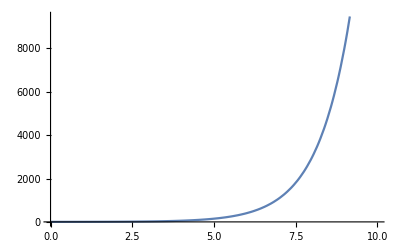

```mathematica
Plot[{Sinh[x]+ Cosh[x]}, {x, 0, 10}]
```

```mathematica
Series[%108, {ep, 0, 2}]
```

((r x0-xx0-2 T λ σξ^2 K1'[0]) ep+(2 xh0+8 r T λ σξ^2 K1'[0]) ep^2+O[ep]^3)+Cosh[(T λ)/ep-2 (r T λ)-2 (r^2 T λ) ep-4 (r^3 T λ) ep^2+O[ep]^3] ((-r x0+xx0-T xh0 λ+2 r T xx0 λ+2 T λ σξ^2 K1'[0]) ep+(-2 xh0+4 r T xh0 λ-8 r^2 T xx0 λ-8 r T λ σξ^2 K1'[0]) ep^2+O[ep]^3)+((-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ) ep+(-2 r xx0-2 r T xh0 λ-2 r (-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ)) ep^2+O[ep]^3) Sinh[(T λ)/ep-2 (r T λ)-2 (r^2 T λ) ep-4 (r^3 T λ) ep^2+O[ep]^3]==T (-r x0+xx0) λ-T (-4 r^2 x0+xh0+4 r xx0) λ ep+4 r T xh0 λ ep^2+O[ep]^3

#### Which terms to keep? Keep to O(ep^2)

```mathematica
Series[√K1[0] √(4 r T λ+K1[0])Cosh[√K1[0] √(4 r T λ+K1[0])]/.K1[0]->T λ/ep, {ep,0,1}]
```

Cosh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2] ((T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2)

```mathematica
Series[√K1[0] √(4 r T λ+K1[0])Cos[√K1[0] √(4 r T λ+K1[0])]/.K1[0]->T λ/ep, {ep,0,1}]
```

Cos[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2] ((T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2)

```mathematica
Series[Cosh[x], {x, 0, 2}]
```

1+x^2/2+O[x]^3

```mathematica
Normal@%122 /. ep->-T*λ/K1[0]
```

-((T^2 λ^2 (-2 r xx0-2 r T xh0 λ-2 r (-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ)))/K1[0]^2-(T λ (-r x0+xx0+T (2 r^2 x0+xh0-2 r xx0) λ))/K1[0]) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-(T λ (r x0-xx0-2 T λ σξ^2 K1'[0]))/K1[0]+(T^2 λ^2 (2 xh0+8 r T λ σξ^2 K1'[0]))/K1[0]^2+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]] (-(T λ (-r x0+xx0-T xh0 λ+2 r T xx0 λ+2 T λ σξ^2 K1'[0]))/K1[0]+(T^2 λ^2 (-2 xh0+4 r T xh0 λ-8 r^2 T xx0 λ-8 r T λ σξ^2 K1'[0]))/K1[0]^2)==T (-r x0+xx0) λ+(4 r T^3 xh0 λ^3)/K1[0]^2+(T^2 (-4 r^2 x0+xh0+4 r xx0) λ^2)/K1[0]

```mathematica
TrigToExp[Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]]
```

-1/2 ⅇ^(-2 r T λ-(4 r^3 T^3 λ^3)/K1[0]^2+(2 r^2 T^2 λ^2)/K1[0]-K1[0])+1/2 ⅇ^(2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0])

```mathematica
TrigToExp[Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]]
```

1/2 ⅇ^(-2 r T λ-(4 r^3 T^3 λ^3)/K1[0]^2+(2 r^2 T^2 λ^2)/K1[0]-K1[0])+1/2 ⅇ^(2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0])

#### Solve by power in K1[0]

```mathematica
Solve[T (-r x0+xx0) λ==0, xx0]
```

{{xx0→r x0}}

```mathematica
%137/.{xx0->r x0}
```

-((T^2 λ^2 (-2 r^2 x0-4 r T xh0 λ))/K1[0]^2-(T^2 xh0 λ^2)/K1[0]) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+(2 T^2 λ^2 σξ^2 K1'[0])/K1[0]+(T^2 λ^2 (2 xh0+8 r T λ σξ^2 K1'[0]))/K1[0]^2+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]] (-(T λ (2 r^2 T x0 λ-T xh0 λ+2 T λ σξ^2 K1'[0]))/K1[0]+(T^2 λ^2 (-2 xh0-8 r^3 T x0 λ+4 r T xh0 λ-8 r T λ σξ^2 K1'[0]))/K1[0]^2)==(4 r T^3 xh0 λ^3)/K1[0]^2+(T^2 xh0 λ^2)/K1[0]

```mathematica
FullSimplify[Solve[-((T^2 λ^2 (-2 r^2 x0-4 r T xh0 λ))/K1[0]^2) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+(T^2 λ^2 (2 xh0+8 r T λ σξ^2 K1'[0]))/K1[0]^2+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]] ((T^2 λ^2 (-2 xh0-8 r^3 T x0 λ+4 r T xh0 λ-8 r T λ σξ^2 K1'[0]))/K1[0]^2)==(4 r T^3 xh0 λ^3)/K1[0]^2,K1'[0]]]
```

{{K1'[0]→(xh0-2 r T xh0 λ+(-xh0+2 r T (-2 r^2 x0+xh0) λ) Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+r (r x0+2 T xh0 λ) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])/(4 r T λ σξ^2 (-1+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))}}

```mathematica
FullSimplify[Solve[(T^2 xh0 λ^2) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+2 T^2 λ^2 σξ^2 K1'[0]+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]] (-T λ (2 r^2 T x0 λ-T xh0 λ+2 T λ σξ^2 K1'[0]))==T^2 xh0 λ^2, K1'[0]]]
```

{{K1'[0]→((-2 r^2 x0+xh0) Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+xh0 (-1+Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))}}

```mathematica
Solve[((-2 r^2 x0+xh0) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+xh0 (-1+Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))==(xh0-2 r T xh0 λ+(-xh0+2 r T (-2 r^2 x0+xh0) λ) Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+r (r x0+2 T xh0 λ) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])/(4 r T λ σξ^2 (-1+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])), K1[0]]
```

$Aborted

```mathematica
Cosh[x+y]
```

Cosh[x+y]

```mathematica
TrigToExp[%]
```

ⅇ^(-x-y)/2+ⅇ^(x+y)/2

```mathematica
TrigToExp[((-2 r^2 x0+xh0) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+xh0 (-1+Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))]
```

((-1+1/2 (-ⅇ^(-2 r T λ+(2 r^2 T^2 λ^2)/K1[0]-K1[0])+ⅇ^(2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]))) xh0+1/2 (ⅇ^(-2 r T λ+(2 r^2 T^2 λ^2)/K1[0]-K1[0])+ⅇ^(2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0])) (-2 r^2 x0+xh0))/(2 (-1+1/2 (ⅇ^(-2 r T λ+(2 r^2 T^2 λ^2)/K1[0]-K1[0])+ⅇ^(2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]))) σξ^2)

```mathematica
FullSimplify[%]
```

(-ⅇ^((4 r^2 T^2 λ^2)/K1[0]) r^2 x0-ⅇ^(2 r T λ+(2 r^2 T^2 λ^2)/K1[0]+K1[0]) xh0+ⅇ^(4 r T λ+2 K1[0]) (-r^2 x0+xh0))/((ⅇ^((2 r^2 T^2 λ^2)/K1[0])-ⅇ^(2 r T λ+K1[0]))^2 σξ^2)

```mathematica
FullSimplify[TrigToExp[(xh0-2 r T xh0 λ+(-xh0+2 r T (-2 r^2 x0+xh0) λ) Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+r (r x0+2 T xh0 λ) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])/(4 r T λ σξ^2 (-1+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))]]
```

-(2 ⅇ^(((2 r T λ+K1[0]) (2 r^2 T^2 λ^2+K1[0]^2))/K1[0]^2) xh0 (-1+2 r T λ)+ⅇ^(4 r T λ+(8 r^3 T^3 λ^3)/K1[0]^2+2 K1[0]) (r^2 x0-xh0) (-1+4 r T λ)+ⅇ^((4 r^2 T^2 λ^2)/K1[0]) (xh0+r^2 x0 (1+4 r T λ)))/(4 (ⅇ^((2 r^2 T^2 λ^2)/K1[0])-ⅇ^(2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2+K1[0]))^2 r T λ σξ^2)

```mathematica
Solve[%157==%156, K1[0]]
```

$Aborted

```mathematica
Solve[((-2 r^2 x0+xh0) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+xh0 (-1+Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))==(xh0-2 r T xh0 λ+(-xh0+2 r T (-2 r^2 x0+xh0) λ) Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+r (r x0+2 T xh0 λ) Sinh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])/(4 r T λ σξ^2 (-1+Cosh[2 r T λ+(4 r^3 T^3 λ^3)/K1[0]^2-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])), K1[0]]
```

```mathematica
%/.K1'[0]->λ/ep
```

T λ (T xh0 λ-(2 T λ^2 σξ^2)/ep)+T λ (2 r^2 T x0 λ-T xh0 λ+(2 T λ^2 σξ^2)/ep) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-T^2 xh0 λ^2 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]==0

```mathematica
Series[%, {ep,0,1}]
```

(-2 T^2 λ^3 σξ^2+2 T^2 λ^3 σξ^2 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])/ep+(T^2 xh0 λ^2+T λ (2 r^2 T x0 λ-T xh0 λ) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-T^2 xh0 λ^2 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])+O[ep]^2==0

```mathematica
Normal@%
```

T^2 xh0 λ^2+T λ (2 r^2 T x0 λ-T xh0 λ) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+(-2 T^2 λ^3 σξ^2+2 T^2 λ^3 σξ^2 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])/ep-T^2 xh0 λ^2 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]==0

```mathematica
%/.ep->λ/K1'[0]
```

T^2 xh0 λ^2+T λ (2 r^2 T x0 λ-T xh0 λ) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-T^2 xh0 λ^2 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+((-2 T^2 λ^3 σξ^2+2 T^2 λ^3 σξ^2 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]) K1'[0])/λ==0

```mathematica
FullSimplify[Solve[%90, K1'[0]]]
```

{{K1'[0]→((-2 r^2 x0+xh0) Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]+xh0 (-1+Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]))}}

```mathematica
K1'[0]->((-2 r^2 x0+xh0) Cosh[2 r T λ+K1[0]]+xh0 (-1+Sinh[2 r T λ+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ+K1[0]]))
```

```mathematica
Limit[((-2 r^2 x0+xh0) Cosh[2 r T λ+K1[0]]+xh0 (-1+Sinh[2 r T λ+K1[0]]))/(2 σξ^2 (-1+Cosh[2 r T λ+K1[0]])), K1[0]->-Infinity]
```

-(r^2 x0)/σξ^2

```mathematica
g
```

```mathematica
TrigToExp[%74]
```

{{K1'[0]→((-1+1/2 (-ⅇ^(-K1[0])+ⅇ^K1[0])) xh0+1/2 (ⅇ^(-K1[0])+ⅇ^K1[0]) (xh0-2 r xx0))/(2 (-1+1/2 (ⅇ^(-K1[0])+ⅇ^K1[0])) σξ^2)}}

```mathematica
FullSimplify[%]
```

{{K1'[0]→(Csch[K1[0]/2]^2 ((xh0-2 r xx0) Cosh[K1[0]]+xh0 (-1+Sinh[K1[0]])))/(4 σξ^2)}}

```mathematica
FullSimplify[%, Assumptions->{xh0>0, x0>0, xx0>0, r>0}]
```

{{K1[0]→ConditionalExpression[2 ⅈ π C[1]+Log[(xh0+√(xh0^2+4 r xh0 xx0-4 r^2 xx0^2))/(2 xh0-2 r xx0)],C[1]∈ℤ]},{K1[0]→ConditionalExpression[2 ⅈ π C[1]+Log[(xh0-√(xh0^2+4 r xh0 xx0-4 r^2 xx0^2))/(2 xh0-2 r xx0)],C[1]∈ℤ]}}

```mathematica
FullSimplify[ Cosh[Log[(xh0+√(xh0^2+4 r xh0 xx0-4 r^2 xx0^2))/(2 xh0-2 r xx0)]]]
```

(2 xh0)/(xh0-2 r xx0+√(xh0^2+4 r xh0 xx0-4 r^2 xx0^2))

```mathematica
Solve[((-2 T^2 λ^3 σξ^2+2 T^2 λ^3 σξ^2 Cosh[Log[(xh0+√(xh0^2+4 r xh0 xx0-4 r^2 xx0^2))/(2 xh0-2 r xx0)]]) K1'[0])/λ==0, K1'[0]]
```

{{K1'[0]→0}}

```mathematica
Limit[%
```

```mathematica
Solve[s0==b0, K1[0]]
```

$Aborted

```mathematica
1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-2 T λ (T xh0 λ+(-r x0+xx0) K1[0])+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2)-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])-(ⅇ^K1[0] 4 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])])  T^2 λ^2 σξ^2 K1'[0])/(K1[0] (4 r T λ+K1[0]))==0
```

1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-2 T λ (T xh0 λ+(-r x0+xx0) K1[0])+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2)-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])-(4 ⅇ^K1[0] T^2 λ^2 σξ^2 (-1+Cosh[√K1[0] √(4 r T λ+K1[0])]) K1'[0])/(K1[0] (4 r T λ+K1[0]))==0

```mathematica
FullSimplify[%]
```

1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))==0

```mathematica
Collect[%, {Sinh[√K1[0] √(4 r T λ+K1[0])], Cosh[√K1[0] √(4 r T λ+K1[0])]}]
```

-(ⅇ^K1[0] (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])/(√K1[0] √(4 r T λ+K1[0]))-(2 ⅇ^K1[0] T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0])))/(K1[0] (4 r T λ+K1[0]))+(ⅇ^K1[0] Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))/(K1[0] (4 r T λ+K1[0]))==0

```mathematica
FullSimplify[%17, Assumptions->{K1[0]<0, 4*r*T*λ>0}]
```

1/(4 r T λ+K1[0])(-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))==0

```mathematica
%/.K1[0]->T*λ/ep
```

1/((T λ)/ep+4 r T λ)(-√((T λ)/ep) √((T λ)/ep+4 r T λ) ((T x0 λ)/ep+2 T xx0 λ) Sinh[√((T λ)/ep) √((T λ)/ep+4 r T λ)]-2 T λ ((T (-r x0+xx0) λ)/ep+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√((T λ)/ep) √((T λ)/ep+4 r T λ)] ((T^2 x0 λ^2)/ep^2+(2 T^2 (r x0+xx0) λ^2)/ep+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))==0

```mathematica
Series[%, {ep, 0, 1}]
```

Cosh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^(3/2)] ((T x0 λ)/ep+O[ep]^0)+(-2 (T (-r x0+xx0) λ)+O[ep]^1)+(-(T x0 λ)/ep+O[ep]^0) Sinh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2]==0

```mathematica
Normal@%
```

-2 T (-r x0+xx0) λ+(T x0 λ Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ])/ep-(T x0 λ Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ])/ep==0

```mathematica
%/.ep->T*λ/c0
```

-2 T (-r x0+xx0) λ+c0 x0 Cosh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]-c0 x0 Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]==0

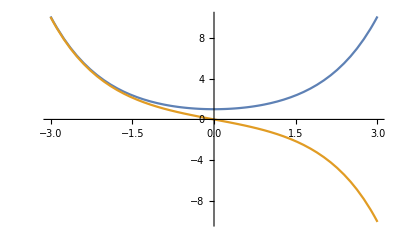

```mathematica
Plot[{Cosh[x], -Sinh[x]}, {x, -3, 3}]
```

```mathematica
Normal@Series[%,
```

```mathematica
%188 /. K1[0]->c0
```

-2 T λ (c0 (-r x0+xx0)+T xh0 λ)+(c0^2 x0+2 c0 T (r x0+xx0) λ+2 T^2 xh0 λ^2) Cosh[√c0 √(c0+4 r T λ)]-√c0 √(c0+4 r T λ) (c0 x0+2 T xx0 λ) Sinh[√c0 √(c0+4 r T λ)]-2 ⅇ^(-√c0 √(c0+4 r T λ)) (-1+ⅇ^(√c0 √(c0+4 r T λ)))^2 T^2 λ^2 σξ^2 K1'[0]==0

```mathematica
%189/.c0->T λ/ep
```

-2 T λ (T xh0 λ+(T (-r x0+xx0) λ)/ep)+((T^2 x0 λ^2)/ep^2+2 T^2 xh0 λ^2+(2 T^2 (r x0+xx0) λ^2)/ep) Cosh[√((T λ)/ep) √((T λ)/ep+4 r T λ)]-√((T λ)/ep) √((T λ)/ep+4 r T λ) ((T x0 λ)/ep+2 T xx0 λ) Sinh[√((T λ)/ep) √((T λ)/ep+4 r T λ)]-2 ⅇ^(-√((T λ)/ep) √((T λ)/ep+4 r T λ)) (-1+ⅇ^(√((T λ)/ep) √((T λ)/ep+4 r T λ)))^2 T^2 λ^2 σξ^2 K1'[0]==0

```mathematica
Series[%, {ep, 0, 1}]
```

Cosh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^(3/2)] ((T^2 x0 λ^2)/ep^2+(2 T^2 (r x0+xx0) λ^2)/ep+2 T^2 xh0 λ^2+O[ep]^2)+(-(2 (T^2 (-r x0+xx0) λ^2))/ep+(-2 T^2 xh0 λ^2+4 T^2 λ^2 σξ^2 K1'[0])+O[ep]^(3/2))+(-(T^2 x0 λ^2)/ep^2+(-2 r T^2 x0 λ^2-2 T^2 xx0 λ^2)/ep+(2 r^2 T^2 x0 λ^2-4 r T^2 xx0 λ^2)+(-4 r^3 T^2 x0 λ^2+4 r^2 T^2 xx0 λ^2) ep+O[ep]^2) Sinh[(T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^2]-2 ⅇ^(-(T λ)/ep-2 (r T λ)+2 r^2 T λ ep+O[ep]^(3/2)) T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^((T λ)/ep+2 r T λ-2 (r^2 T λ) ep+O[ep]^(3/2)) T^2 λ^2 σξ^2 K1'[0]==0

```mathematica
Normal@%194
```

-2 T^2 xh0 λ^2-(2 T^2 (-r x0+xx0) λ^2)/ep+((T^2 x0 λ^2)/ep^2+2 T^2 xh0 λ^2+(2 T^2 (r x0+xx0) λ^2)/ep) Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]+(-(T^2 x0 λ^2)/ep^2+2 r^2 T^2 x0 λ^2-4 r T^2 xx0 λ^2+(-2 r T^2 x0 λ^2-2 T^2 xx0 λ^2)/ep+ep (-4 r^3 T^2 x0 λ^2+4 r^2 T^2 xx0 λ^2)) Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]+4 T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^((T λ)/ep+2 r T λ-2 ep r^2 T λ) T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(-(T λ)/ep-2 r T λ+2 ep r^2 T λ) T^2 λ^2 σξ^2 K1'[0]==0

```mathematica
Collect[%197, ep]
```

-2 T^2 xh0 λ^2+2 T^2 xh0 λ^2 Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]+2 r^2 T^2 x0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]-4 r T^2 xx0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]+(T^2 x0 λ^2 Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]-T^2 x0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ])/ep^2+1/ep(2 r T^2 x0 λ^2-2 T^2 xx0 λ^2+2 r T^2 x0 λ^2 Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]+2 T^2 xx0 λ^2 Cosh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]-2 r T^2 x0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]-2 T^2 xx0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ])+ep (-4 r^3 T^2 x0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ]+4 r^2 T^2 xx0 λ^2 Sinh[(T λ)/ep+2 r T λ-2 ep r^2 T λ])+4 T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^((T λ)/ep+2 r T λ-2 ep r^2 T λ) T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(-(T λ)/ep-2 r T λ+2 ep r^2 T λ) T^2 λ^2 σξ^2 K1'[0]==0

```mathematica
%197/.ep->T λ/c0
```

-2 c0 T (-r x0+xx0) λ-2 T^2 xh0 λ^2+(c0^2 x0+2 c0 T (r x0+xx0) λ+2 T^2 xh0 λ^2) Cosh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]+(-c0^2 x0+2 r^2 T^2 x0 λ^2-4 r T^2 xx0 λ^2+(c0 (-2 r T^2 x0 λ^2-2 T^2 xx0 λ^2))/(T λ)+(T λ (-4 r^3 T^2 x0 λ^2+4 r^2 T^2 xx0 λ^2))/c0) Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]+4 T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(c0+2 r T λ-(2 r^2 T^2 λ^2)/c0) T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(-c0-2 r T λ+(2 r^2 T^2 λ^2)/c0) T^2 λ^2 σξ^2 K1'[0]==0

```mathematica
Collect[%, c0]
```

-2 T^2 xh0 λ^2+2 T^2 xh0 λ^2 Cosh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]+2 r^2 T^2 x0 λ^2 Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]-4 r T^2 xx0 λ^2 Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]+c0^2 (x0 Cosh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]-x0 Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0])+c0 (2 r T x0 λ-2 T xx0 λ+2 r T x0 λ Cosh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]+2 T xx0 λ Cosh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]-2 r T x0 λ Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]-2 T xx0 λ Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0])+(-4 r^3 T^3 x0 λ^3 Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0]+4 r^2 T^3 xx0 λ^3 Sinh[c0+2 r T λ-(2 r^2 T^2 λ^2)/c0])/c0+4 T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(c0+2 r T λ-(2 r^2 T^2 λ^2)/c0) T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(-c0-2 r T λ+(2 r^2 T^2 λ^2)/c0) T^2 λ^2 σξ^2 K1'[0]==0

#### Solve term by term in the series

```mathematica
Solve[(x0 Cosh[c0+2 r T λ]-x0 Sinh[c0+2 r T λ])==0, c0]
```

{}

```mathematica
Limit[(x0 Cosh[c0+2 r T λ]-x0 Sinh[c0+2 r T λ]), c0->-Infinity]
```

ComplexInfinity

#### Get initial cost in a series in small T*l /K1(0)

```mathematica
1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-2 T λ (T xh0 λ+(-r x0+xx0) K1[0])+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2)-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])-((2 ⅇ^(K1[0]-√K1[0] √(4 r T λ+K1[0])) (-1+ⅇ^(√K1[0] √(4 r T λ+K1[0])))^2 T^2 λ^2 σξ^2 K1'[0])/(K1[0] (4 r T λ+K1[0])))
```

1/(K1[0] (4 r T λ+K1[0]))ⅇ^K1[0] (-2 T λ (T xh0 λ+(-r x0+xx0) K1[0])+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2)-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])])-(2 ⅇ^(K1[0]-√K1[0] √(4 r T λ+K1[0])) (-1+ⅇ^(√K1[0] √(4 r T λ+K1[0])))^2 T^2 λ^2 σξ^2 K1'[0])/(K1[0] (4 r T λ+K1[0]))

```mathematica
FullSimplify[%*K1[0] (4 r T λ+K1[0])]
```

ⅇ^K1[0] (-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))

```mathematica
FullSimplify[%/ⅇ^K1[0]]
```

-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
%128/.K1[0]->c
```

-√c √(c+4 r T λ) (c x0+2 T xx0 λ) Sinh[√c √(c+4 r T λ)]-2 T λ (c (-r x0+xx0)+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√c √(c+4 r T λ)] (c^2 x0+2 c T (r x0+xx0) λ+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
%148/c^2
```

1/c^2(-√c √(c+4 r T λ) (c x0+2 T xx0 λ) Sinh[√c √(c+4 r T λ)]-2 T λ (c (-r x0+xx0)+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√c √(c+4 r T λ)] (c^2 x0+2 c T (r x0+xx0) λ+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))

```mathematica
FullSimplify[%151, Assumptions->{c>0, r>0, T>0,  λ>0}]
```

1/c^2(-√(c (c+4 r T λ)) (c x0+2 T xx0 λ) Sinh[√(c (c+4 r T λ))]-2 T λ (c (-r x0+xx0)+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√(c (c+4 r T λ))] (c^2 x0+2 c T (r x0+xx0) λ+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])))

```mathematica
Expand[%153]
```

(2 r T x0 λ)/c-(2 T xx0 λ)/c-(2 T^2 xh0 λ^2)/c^2+x0 Cosh[√(c (c+4 r T λ))]+(2 r T x0 λ Cosh[√(c (c+4 r T λ))])/c+(2 T xx0 λ Cosh[√(c (c+4 r T λ))])/c+(2 T^2 xh0 λ^2 Cosh[√(c (c+4 r T λ))])/c^2-(x0 √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c-(2 T xx0 λ √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c^2+(4 T^2 λ^2 σξ^2 K1'[0])/c^2-(4 T^2 λ^2 σξ^2 Cosh[√(c (c+4 r T λ))] K1'[0])/c^2

```mathematica
x0 Cosh[√(c (c+4 r T λ))]+(2 r T x0 λ Cosh[√(c (c+4 r T λ))])/c+(2 T xx0 λ Cosh[√(c (c+4 r T λ))])/c+(2 T^2 xh0 λ^2 Cosh[√(c (c+4 r T λ))])/c^2-(x0 √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c-(2 T xx0 λ √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c^2+4 T^2 λ^2 σξ^2 K1'[0]-(4 T^2 λ^2 σξ^2 Cosh[√(c (c+4 r T λ))] K1'[0])/c^2
```

x0 Cosh[√(c (c+4 r T λ))]+(2 r T x0 λ Cosh[√(c (c+4 r T λ))])/c+(2 T xx0 λ Cosh[√(c (c+4 r T λ))])/c+(2 T^2 xh0 λ^2 Cosh[√(c (c+4 r T λ))])/c^2-(x0 √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c-(2 T xx0 λ √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c^2+4 T^2 λ^2 σξ^2 K1'[0]-(4 T^2 λ^2 σξ^2 Cosh[√(c (c+4 r T λ))] K1'[0])/c^2

```mathematica
Limit[(2 T xx0 λ √(c (c+4 r T λ)) Sinh[√(c (c+4 r T λ))])/c^2+(2 T xx0 λ Cosh[√(c (c+4 r T λ))])/c, c->Infinity]
```

ComplexInfinity

```mathematica
%==0
```

-√c √(c+4 r T λ) (c x0+2 T xx0 λ) Sinh[√c √(c+4 r T λ)]-2 T λ (c (-r x0+xx0)+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√c √(c+4 r T λ)] (c^2 x0+2 c T (r x0+xx0) λ+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))==0

```mathematica
%/c^2
```

1/c^2(-√c √(c+4 r T λ) (c x0+2 T xx0 λ) Sinh[√c √(c+4 r T λ)]-2 T λ (c (-r x0+xx0)+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√c √(c+4 r T λ)] (c^2 x0+2 c T (r x0+xx0) λ+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))==0)

```mathematica
TrigToExp[%]
```

-1/2 (-ⅇ^(-√K1[0] √(4 r T λ+K1[0]))+ⅇ^(√K1[0] √(4 r T λ+K1[0]))) √K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0])-2 T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0]))+1/2 (ⅇ^(-√K1[0] √(4 r T λ+K1[0]))+ⅇ^(√K1[0] √(4 r T λ+K1[0]))) (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
Expand[%]
```

-2 T^2 xh0 λ^2+ⅇ^(-√K1[0] √(4 r T λ+K1[0])) T^2 xh0 λ^2+ⅇ^(√K1[0] √(4 r T λ+K1[0])) T^2 xh0 λ^2+2 r T x0 λ K1[0]+ⅇ^(-√K1[0] √(4 r T λ+K1[0])) r T x0 λ K1[0]+ⅇ^(√K1[0] √(4 r T λ+K1[0])) r T x0 λ K1[0]-2 T xx0 λ K1[0]+ⅇ^(-√K1[0] √(4 r T λ+K1[0])) T xx0 λ K1[0]+ⅇ^(√K1[0] √(4 r T λ+K1[0])) T xx0 λ K1[0]+1/2 ⅇ^(-√K1[0] √(4 r T λ+K1[0])) x0 K1[0]^2+1/2 ⅇ^(√K1[0] √(4 r T λ+K1[0])) x0 K1[0]^2+ⅇ^(-√K1[0] √(4 r T λ+K1[0])) T xx0 λ √K1[0] √(4 r T λ+K1[0])-ⅇ^(√K1[0] √(4 r T λ+K1[0])) T xx0 λ √K1[0] √(4 r T λ+K1[0])+1/2 ⅇ^(-√K1[0] √(4 r T λ+K1[0])) x0 K1[0]^(3/2) √(4 r T λ+K1[0])-1/2 ⅇ^(√K1[0] √(4 r T λ+K1[0])) x0 K1[0]^(3/2) √(4 r T λ+K1[0])+4 T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(-√K1[0] √(4 r T λ+K1[0])) T^2 λ^2 σξ^2 K1'[0]-2 ⅇ^(√K1[0] √(4 r T λ+K1[0])) T^2 λ^2 σξ^2 K1'[0]

```mathematica
FullSimplify[%]
```

-√K1[0] √(4 r T λ+K1[0]) (2 T xx0 λ+x0 K1[0]) Sinh[√K1[0] √(4 r T λ+K1[0])]-2 T λ ((-r x0+xx0) K1[0]+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√K1[0] √(4 r T λ+K1[0])] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
%/.K1[0]->-λ*T/ep
```

-√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ) (-(T x0 λ)/ep+2 T xx0 λ) Sinh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)]-2 T λ (-(T (-r x0+xx0) λ)/ep+T λ (xh0-2 σξ^2 K1'[0]))+Cosh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)] ((T^2 x0 λ^2)/ep^2-(2 T^2 (r x0+xx0) λ^2)/ep+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
Series[%, {ep, 0, 1}]
```

((2 T^2 (-r x0+xx0) λ^2)/ep-2 (T^2 λ^2 (xh0-2 σξ^2 K1'[0]))+O[ep]^2)+Cosh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^(3/2)] ((T^2 x0 λ^2)/ep^2-(2 (T^2 (r x0+xx0) λ^2))/ep+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])+O[ep]^2)+(-(T^2 x0 λ^2)/ep^2+(2 r T^2 x0 λ^2+2 T^2 xx0 λ^2)/ep+(2 r^2 T^2 x0 λ^2-4 r T^2 xx0 λ^2)+(4 r^3 T^2 x0 λ^2-4 r^2 T^2 xx0 λ^2) ep+O[ep]^2) Sinh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2]

```mathematica
FullSimplify[%]
```

((2 T^2 (-r x0+xx0) λ^2)/ep-2 (T^2 λ^2 (xh0-2 σξ^2 K1'[0]))+O[ep]^2)+Cosh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^(3/2)] ((T^2 x0 λ^2)/ep^2-(2 (T^2 (r x0+xx0) λ^2))/ep+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])+O[ep]^2)+(-(T^2 x0 λ^2)/ep^2+(2 T^2 (r x0+xx0) λ^2)/ep+2 r T^2 (r x0-2 xx0) λ^2+4 r^2 T^2 (r x0-xx0) λ^2 ep+O[ep]^2) Sinh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2]

```mathematica
Normal@%134
```

(2 T^2 (-r x0+xx0) λ^2)/ep-(-(T^2 x0 λ^2)/ep^2+2 r T^2 (r x0-2 xx0) λ^2+4 ep r^2 T^2 (r x0-xx0) λ^2+(2 T^2 (r x0+xx0) λ^2)/ep) Sinh[(T λ)/ep-2 r T λ-2 ep r^2 T λ]-2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])+Cosh[(T λ)/ep-2 r T λ-2 ep r^2 T λ] ((T^2 x0 λ^2)/ep^2-(2 T^2 (r x0+xx0) λ^2)/ep+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
%/.ep->-λ*T/K1[0]
```

-2 T (-r x0+xx0) λ K1[0]+(2 r T^2 (r x0-2 xx0) λ^2-(4 r^2 T^3 (r x0-xx0) λ^3)/K1[0]-2 T (r x0+xx0) λ K1[0]-x0 K1[0]^2) Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])+Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
FullSimplify[%]
```

2 T (r x0-xx0) λ K1[0]+(2 r T^2 (r x0-2 xx0) λ^2+(4 r^2 T^3 (-r x0+xx0) λ^3)/K1[0]-2 T (r x0+xx0) λ K1[0]-x0 K1[0]^2) Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])+Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]] (2 T (r x0+xx0) λ K1[0]+x0 K1[0]^2+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
(-x0 K1[0]^2) Sinh[K1[0]]+Cosh[K1[0]] (x0 K1[0]^2)==0
```

x0 Cosh[K1[0]] K1[0]^2-x0 K1[0]^2 Sinh[K1[0]]==0

```mathematica
TrigToExp[%143]
```

ⅇ^(-K1[0]) x0 K1[0]^2==0

```mathematica
%137/.K1[0]->c
```

-2 c T (-r x0+xx0) λ+(-c^2 x0-2 c T (r x0+xx0) λ+2 r T^2 (r x0-2 xx0) λ^2-(4 r^2 T^3 (r x0-xx0) λ^3)/c) Sinh[c+2 r T λ-(2 r^2 T^2 λ^2)/c]-2 T^2 λ^2 (xh0-2 σξ^2 K1'[0])+Cosh[c+2 r T λ-(2 r^2 T^2 λ^2)/c] (c^2 x0+2 c T (r x0+xx0) λ+2 T^2 λ^2 (xh0-2 σξ^2 K1'[0]))

```mathematica
Limit[%, c->Infinity]
```

ConditionalExpression[-∞,T^2 λ^2 (r^2 x0+xh0-2 r xx0-2 σξ^2 K1'[0])<0]

```mathematica
Solve[%, K1[0]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{K1[0]→0}}

```mathematica
%71/.K1[0]->-λ*T/ep
```

-1/(T λ (-(T λ)/ep+4 r T λ))ⅇ^(-(T λ)/ep) ep (-2 T λ (T xh0 λ-(T (-r x0+xx0) λ)/ep)+((T^2 x0 λ^2)/ep^2+2 T^2 xh0 λ^2-(2 T^2 (r x0+xx0) λ^2)/ep) Cosh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)]-√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ) (-(T x0 λ)/ep+2 T xx0 λ) Sinh[√(-(T λ)/ep) √(-(T λ)/ep+4 r T λ)])

```mathematica
Series[%73, {ep, 0, 2}]
```

ⅇ^(-(T λ)/ep+O[ep]^3) (Cosh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2] (x0+2 (r x0-xx0) ep+O[ep]^2)+(2 (-r x0+xx0) ep+(-2 xh0+8 r (-r x0+xx0)) ep^2+O[ep]^3)+(-x0-2 (r x0-xx0) ep+O[ep]^2) Sinh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2])

```mathematica
Expand[%78]
```

ⅇ^(-(T λ)/ep+O[ep]^3) Cosh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2] (x0+2 (r x0-xx0) ep+O[ep]^2)+ⅇ^(-(T λ)/ep+O[ep]^3) (2 (-r x0+xx0) ep+(-2 xh0+8 r (-r x0+xx0)) ep^2+O[ep]^3)+ⅇ^(-(T λ)/ep+O[ep]^3) (-x0-2 (r x0-xx0) ep+O[ep]^2) Sinh[-(T λ)/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2]

```mathematica
TrigToExp[%]
```

ⅇ^(-(2 (T λ))/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2) (x0/2+(r x0-xx0) ep+O[ep]^2)+ⅇ^(-(T λ)/ep+O[ep]^3) (2 (-r x0+xx0) ep+(-2 xh0+8 r (-r x0+xx0)) ep^2+O[ep]^3)+ⅇ^(-(2 (T λ))/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2) (-x0/2+(-r x0+xx0) ep+O[ep]^2)+(ⅇ^(-2 r T λ) x0+(ⅇ^(-2 r T λ) (r x0-xx0)-ⅇ^(-2 r T λ) (-r x0+xx0)-2 ⅇ^(-2 r T λ) r^2 T x0 λ) ep+O[ep]^2)

```mathematica
FullSimplify[%]
```

ⅇ^(-(2 (T λ))/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2) O[ep]^2+ⅇ^(-(T λ)/ep+O[ep]^3) (2 (-r x0+xx0) ep+(-2 xh0+8 r (-r x0+xx0)) ep^2+O[ep]^3)+(ⅇ^(-2 r T λ) x0-2 (ⅇ^(-2 r T λ) (xx0+r x0 (-1+r T λ))) ep+O[ep]^2)

```mathematica
Collect[%81, {ep}]
```

ⅇ^(-(2 (T λ))/ep+2 r T λ+2 r^2 T λ ep+O[ep]^2) O[ep]^2+ⅇ^(-(T λ)/ep+O[ep]^3) (2 (-r x0+xx0) ep+(-2 xh0+8 r (-r x0+xx0)) ep^2+O[ep]^3)+(ⅇ^(-2 r T λ) x0-2 (ⅇ^(-2 r T λ) (xx0+r x0 (-1+r T λ))) ep+O[ep]^2)

```mathematica
Normal@%
```

ⅇ^(-2 r T λ) x0+ⅇ^(-(T λ)/ep) (2 ep (-r x0+xx0)+ep^2 (-2 xh0+8 r (-r x0+xx0)))-2 ⅇ^(-2 r T λ) ep (xx0+r x0 (-1+r T λ))

```mathematica
FullSimplify[ⅇ^(-2 r T λ) x0+ⅇ^(-(T λ)/ep) (2 ep (-r x0+xx0))-2 ⅇ^(-2 r T λ) ep (xx0+r x0 (-1+r T λ))]
```

2 ⅇ^(-(T λ)/ep) ep (-r x0+xx0)+ⅇ^(-2 r T λ) (x0-2 ep xx0-2 ep r x0 (-1+r T λ))

```mathematica
ExpToTrig[%]
```

2 ep (-r x0+xx0) (Cosh[(T λ)/ep]-Sinh[(T λ)/ep])+(x0+2 ep r x0-2 ep xx0-2 ep r^2 T x0 λ) (Cosh[2 r T λ]-Sinh[2 r T λ])

```mathematica
%/.ep->-λ*T/K1[0]
```

(x0-(2 r T x0 λ)/K1[0]+(2 T xx0 λ)/K1[0]+(2 r^2 T^2 x0 λ^2)/K1[0]) (Cosh[2 r T λ]-Sinh[2 r T λ])-(2 T (-r x0+xx0) λ (Cosh[K1[0]]+Sinh[K1[0]]))/K1[0]

```mathematica
FullSimplify[%]
```

(2 ⅇ^K1[0] T (r x0-xx0) λ+ⅇ^(-2 r T λ) (2 T λ (xx0+r x0 (-1+r T λ))+x0 K1[0]))/K1[0]

```mathematica
Expand[%]
```

ⅇ^(-2 r T λ) x0-(2 ⅇ^(-2 r T λ) r T x0 λ)/K1[0]+(2 ⅇ^K1[0] r T x0 λ)/K1[0]+(2 ⅇ^(-2 r T λ) T xx0 λ)/K1[0]-(2 ⅇ^K1[0] T xx0 λ)/K1[0]+(2 ⅇ^(-2 r T λ) r^2 T^2 x0 λ^2)/K1[0]

#### Get boundary condition by combining initial cost with boundary term from variation (see below)

```mathematica
Solve[ⅇ^K1[0] (x0 Cosh[2 r T λ+K1[0]]-x0 Sinh[2 r T λ+K1[0]])==-2 ⅇ^(-2 r T λ-K1[0]) (-1+ⅇ^(2 r T λ+K1[0])) λ σξ^2 (-K1[0]+r T λ K1[0]-T K1'[0]+ⅇ^(2 r T λ+K1[0]) ((1+r T λ) K1[0]-T (-1+K1[0]) K1'[0])), K1[0]]
```

$Aborted

#### Write down the Lagrangian and get the Euler-Lagrange equations and the boundary term

```mathematica
L[K1[tp], K1'[tp], tp] = FullSimplify[(MatrixExp[K[tp]].B[tp].Transpose[B[tp]].MatrixExp[Transpose[K[tp]]])[[1,1]]]
```

(ⅇ^(K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2))/(2 K1[tp] (4 r (T-tp) λ+K1[tp]))

```mathematica
D[L[K1[tp], K1'[tp], tp], K1'[tp]]
```

(2 ⅇ^(K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp])/(K1[tp] (4 r (T-tp) λ+K1[tp]))

```mathematica
%/.tp->0
```

(2 ⅇ^(K1[0]-√K1[0] √(4 r T λ+K1[0])) (-1+ⅇ^(√K1[0] √(4 r T λ+K1[0])))^2 T^2 λ^2 σξ^2 K1'[0])/(K1[0] (4 r T λ+K1[0]))

First, expand the Lagrangian as a series in l(T-t’)/K1(t’)

```mathematica
%90/. K1[tp]->λ(tp-T)/ep
```

(ⅇ^(((-T+tp) λ)/ep-√(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep)) ep ((2 (1+ⅇ^(√(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep)))^2 r (T-tp) (-T+tp) λ^2 σg^2)/ep+((1+ⅇ^(2 √(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep))) (-T+tp)^2 λ^2 σg^2)/ep^2-(-1+ⅇ^(2 √(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep))) (((-T+tp) λ)/ep)^(3/2) √(4 r (T-tp) λ+((-T+tp) λ)/ep) σg^2+2 (-1+ⅇ^(√(((-T+tp) λ)/ep) √(4 r (T-tp) λ+((-T+tp) λ)/ep)))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2))/(2 (-T+tp) λ (4 r (T-tp) λ+((-T+tp) λ)/ep))

```mathematica
ExpToTrig[%]
```

(ep (Cosh[(T λ)/ep-(tp λ)/ep+√(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)]-Sinh[(T λ)/ep-(tp λ)/ep+√(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)]) (1/ep 2 r (T-tp) (-T+tp) λ^2 σg^2 (1+Cosh[√(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)]+Sinh[√(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)])^2-(-(T λ)/ep+(tp λ)/ep)^(3/2) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ) σg^2 (-1+Cosh[2 √(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)]+Sinh[2 √(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)])+1/ep^2(-T+tp)^2 λ^2 σg^2 (1+Cosh[2 √(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)]+Sinh[2 √(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)])+2 (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)]+Sinh[√(-(T λ)/ep+(tp λ)/ep) √(-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ)])^2 K1'[tp]^2))/(2 (-T+tp) λ (-(T λ)/ep+4 r T λ+(tp λ)/ep-4 r tp λ))

```mathematica
Series[%, {ep, 0,2}]
```

(((Cosh[2 r (T-tp) λ]-Sinh[2 r (T-tp) λ]) ep^2)/(2 (T-tp)^2 λ^2)+O[ep]^(5/2)) (Cosh[-(2 ((T-tp) λ))/ep+4 r (T-tp) λ+4 r^2 (T-tp) λ ep+8 r^3 (T-tp) λ ep^2+O[ep]^(5/2)] (((-T+tp)^2 λ^2 σg^2)/ep^2+O[ep]^3)+Cosh[-(2 ((T-tp) λ))/ep+4 r (T-tp) λ+4 r^2 (T-tp) λ ep+O[ep]^2] (-((T-tp)^2 λ^2 σg^2)/ep^2+(2 r (T-tp)^2 λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2+O[ep]^1)+(((T-tp)^2 λ^2 σg^2+(-T+tp)^2 λ^2 σg^2)/ep^2-(2 (r (T-tp)^2 λ^2 σg^2))/ep-2 (r^2 (T-tp)^2 λ^2 σg^2)+O[ep]^1)+(-((T-tp)^2 λ^2 σg^2)/ep^2+(2 r (T-tp)^2 λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2+O[ep]^1) Sinh[-(2 ((T-tp) λ))/ep+4 r (T-tp) λ+4 r^2 (T-tp) λ ep+O[ep]^2]+(((-T+tp)^2 λ^2 σg^2)/ep^2+O[ep]^3) Sinh[-(2 ((T-tp) λ))/ep+4 r (T-tp) λ+4 r^2 (T-tp) λ ep+8 r^3 (T-tp) λ ep^2+O[ep]^(5/2)]+(-(2 (r (T-tp)^2 λ^2 σg^2))/ep+O[ep]^3) (1+Cosh[-((T-tp) λ)/ep+2 r (T-tp) λ+2 r^2 (T-tp) λ ep+4 r^3 (T-tp) λ ep^2+O[ep]^(5/2)]+Sinh[-((T-tp) λ)/ep+2 r (T-tp) λ+2 r^2 (T-tp) λ ep+4 r^3 (T-tp) λ ep^2+O[ep]^(5/2)])^2+2 (T-tp)^2 λ^2 σξ^2 (-1+Cosh[-((T-tp) λ)/ep+2 r (T-tp) λ+2 r^2 (T-tp) λ ep+4 r^3 (T-tp) λ ep^2+O[ep]^(5/2)]+Sinh[-((T-tp) λ)/ep+2 r (T-tp) λ+2 r^2 (T-tp) λ ep+4 r^3 (T-tp) λ ep^2+O[ep]^(5/2)])^2 K1'[tp]^2)

```mathematica
Normal@%
```

1/(2 (T-tp)^2 λ^2)ep^2 (Cosh[2 r (T-tp) λ]-Sinh[2 r (T-tp) λ]) (-(2 r (T-tp)^2 λ^2 σg^2)/ep-2 r^2 (T-tp)^2 λ^2 σg^2+((T-tp)^2 λ^2 σg^2+(-T+tp)^2 λ^2 σg^2)/ep^2+(-((T-tp)^2 λ^2 σg^2)/ep^2+(2 r (T-tp)^2 λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2) Cosh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]+((-T+tp)^2 λ^2 σg^2 Cosh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ-8 ep^2 r^3 (T-tp) λ])/ep^2-(-((T-tp)^2 λ^2 σg^2)/ep^2+(2 r (T-tp)^2 λ^2 σg^2)/ep+2 r^2 (T-tp)^2 λ^2 σg^2) Sinh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]-((-T+tp)^2 λ^2 σg^2 Sinh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ-8 ep^2 r^3 (T-tp) λ])/ep^2-1/ep 2 r (T-tp)^2 λ^2 σg^2 (1+Cosh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ]-Sinh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ])^2+2 (T-tp)^2 λ^2 σξ^2 (-1+Cosh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ]-Sinh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ])^2 K1'[tp]^2)

```mathematica
Collect[%, ep]
```

1/(2 (T-tp)^2 λ^2)(Cosh[2 r (T-tp) λ]-Sinh[2 r (T-tp) λ]) ((T-tp)^2 λ^2 σg^2+(-T+tp)^2 λ^2 σg^2-(T-tp)^2 λ^2 σg^2 Cosh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]+(-T+tp)^2 λ^2 σg^2 Cosh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ-8 ep^2 r^3 (T-tp) λ]+(T-tp)^2 λ^2 σg^2 Sinh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]-(-T+tp)^2 λ^2 σg^2 Sinh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ-8 ep^2 r^3 (T-tp) λ])+1/(2 (T-tp)^2 λ^2)ep (Cosh[2 r (T-tp) λ]-Sinh[2 r (T-tp) λ]) (-2 r (T-tp)^2 λ^2 σg^2+2 r (T-tp)^2 λ^2 σg^2 Cosh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]-2 r (T-tp)^2 λ^2 σg^2 Sinh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]-2 r (T-tp)^2 λ^2 σg^2 (1+Cosh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ]-Sinh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ])^2)+1/(2 (T-tp)^2 λ^2)ep^2 (Cosh[2 r (T-tp) λ]-Sinh[2 r (T-tp) λ]) (-2 r^2 (T-tp)^2 λ^2 σg^2+2 r^2 (T-tp)^2 λ^2 σg^2 Cosh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]-2 r^2 (T-tp)^2 λ^2 σg^2 Sinh[(2 (T-tp) λ)/ep-4 r (T-tp) λ-4 ep r^2 (T-tp) λ]+2 (T-tp)^2 λ^2 σξ^2 (-1+Cosh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ]-Sinh[((T-tp) λ)/ep-2 r (T-tp) λ-2 ep r^2 (T-tp) λ-4 ep^2 r^3 (T-tp) λ])^2 K1'[tp]^2)

```mathematica
TrigToExp[%]
```

(ⅇ^(-2 r (T-tp) λ) T^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) T^2 σg^2)/(2 (T-tp)^2)+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) T^2 σg^2)/(2 (T-tp)^2)-(2 ⅇ^(-2 r (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep+2 ep r^2 (T-tp) λ+4 ep^2 r^3 (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2-(ⅇ^(-2 r (T-tp) λ) ep^2 r^2 T^2 σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) ep^2 r^2 T^2 σg^2)/(T-tp)^2-(2 ⅇ^(-2 r (T-tp) λ) T tp σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) T tp σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) T tp σg^2)/(T-tp)^2+(4 ⅇ^(-2 r (T-tp) λ) ep r T tp σg^2)/(T-tp)^2-(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) ep r T tp σg^2)/(T-tp)^2+(4 ⅇ^(-((T-tp) λ)/ep+2 ep r^2 (T-tp) λ+4 ep^2 r^3 (T-tp) λ) ep r T tp σg^2)/(T-tp)^2+(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) ep r T tp σg^2)/(T-tp)^2+(2 ⅇ^(-2 r (T-tp) λ) ep^2 r^2 T tp σg^2)/(T-tp)^2-(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) ep^2 r^2 T tp σg^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) tp^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) tp^2 σg^2)/(2 (T-tp)^2)+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) tp^2 σg^2)/(2 (T-tp)^2)-(2 ⅇ^(-2 r (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep+2 ep r^2 (T-tp) λ+4 ep^2 r^3 (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2-(ⅇ^(-2 r (T-tp) λ) ep^2 r^2 tp^2 σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ) ep^2 r^2 tp^2 σg^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep+2 ep r^2 (T-tp) λ+4 ep^2 r^3 (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-2 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2+(4 ⅇ^(-((T-tp) λ)/ep+2 ep r^2 (T-tp) λ+4 ep^2 r^3 (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep+2 ep r^2 (T-tp) λ+4 ep^2 r^3 (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ+4 ep r^2 (T-tp) λ+8 ep^2 r^3 (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2

```mathematica
(ⅇ^(-2 r (T-tp) λ) T^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) T^2 σg^2)/(2 (T-tp)^2)+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) T^2 σg^2)/(2 (T-tp)^2)-(2 ⅇ^(-2 r (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep r T^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2+(2 ⅇ^(-2 r (T-tp) λ) T tp σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) T tp σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) T tp σg^2)/(T-tp)^2+(4 ⅇ^(-2 r (T-tp) λ) ep r T tp σg^2)/(T-tp)^2-(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep r T tp σg^2)/(T-tp)^2+(4 ⅇ^(-((T-tp) λ)/ep) ep r T tp σg^2)/(T-tp)^2+(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep r T tp σg^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) tp^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) tp^2 σg^2)/(2 (T-tp)^2)+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) tp^2 σg^2)/(2 (T-tp)^2)-(2 ⅇ^(-2 r (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep r tp^2 σg^2)/(T-tp)^2-(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-2 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2+(4 ⅇ^(-((T-tp) λ)/ep) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2
```

(ⅇ^(-2 r (T-tp) λ) T^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep r T^2 σg^2)/(T-tp)^2-(2 ⅇ^(-2 r (T-tp) λ) ep r T^2 σg^2)/(T-tp)^2+(2 ⅇ^(-2 r (T-tp) λ) T tp σg^2)/(T-tp)^2+(4 ⅇ^(-((T-tp) λ)/ep) ep r T tp σg^2)/(T-tp)^2+(4 ⅇ^(-2 r (T-tp) λ) ep r T tp σg^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) tp^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep r tp^2 σg^2)/(T-tp)^2-(2 ⅇ^(-2 r (T-tp) λ) ep r tp^2 σg^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep^2 T^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(4 ⅇ^(-((T-tp) λ)/ep) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-2 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep^2 T tp σξ^2 K1'[tp]^2)/(T-tp)^2-(2 ⅇ^(-((T-tp) λ)/ep) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-2 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2+(ⅇ^(-(2 (T-tp) λ)/ep+2 r (T-tp) λ) ep^2 tp^2 σξ^2 K1'[tp]^2)/(T-tp)^2

```mathematica
FullSimplify[%]
```

1/(T-tp)^2 ⅇ^(-(2 (1+ep r) (T-tp) λ)/ep) ((-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) ep r (T-tp)^2+ⅇ^((2 (T-tp) λ)/ep) (T^2-2 ep r T^2+2 T tp+4 ep r T tp+tp^2-2 ep r tp^2)) σg^2+(ⅇ^((2 (T-tp) λ)/ep)+ⅇ^(4 r (T-tp) λ)-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep)) ep^2 (T-tp)^2 σξ^2 K1'[tp]^2)

```mathematica
Collect[%, ep]
```

(ⅇ^(-(2 (1+ep r) (T-tp) λ)/ep) (ⅇ^((2 (T-tp) λ)/ep) T^2 σg^2+2 ⅇ^((2 (T-tp) λ)/ep) T tp σg^2+ⅇ^((2 (T-tp) λ)/ep) tp^2 σg^2))/(T-tp)^2+1/(T-tp)^2 ⅇ^(-(2 (1+ep r) (T-tp) λ)/ep) ep (-2 ⅇ^((2 (T-tp) λ)/ep) r T^2 σg^2-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) r T^2 σg^2+4 ⅇ^((2 (T-tp) λ)/ep) r T tp σg^2+4 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) r T tp σg^2-2 ⅇ^((2 (T-tp) λ)/ep) r tp^2 σg^2-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) r tp^2 σg^2)+1/(T-tp)^2 ⅇ^(-(2 (1+ep r) (T-tp) λ)/ep) ep^2 (ⅇ^((2 (T-tp) λ)/ep) T^2 σξ^2 K1'[tp]^2+ⅇ^(4 r (T-tp) λ) T^2 σξ^2 K1'[tp]^2-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) T^2 σξ^2 K1'[tp]^2-2 ⅇ^((2 (T-tp) λ)/ep) T tp σξ^2 K1'[tp]^2-2 ⅇ^(4 r (T-tp) λ) T tp σξ^2 K1'[tp]^2+4 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) T tp σξ^2 K1'[tp]^2+ⅇ^((2 (T-tp) λ)/ep) tp^2 σξ^2 K1'[tp]^2+ⅇ^(4 r (T-tp) λ) tp^2 σξ^2 K1'[tp]^2-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) tp^2 σξ^2 K1'[tp]^2)

```mathematica
ExpToTrig[%]
```

1/(T-tp)^2(Cosh[(2 (1+ep r) (T-tp) λ)/ep]-Sinh[(2 (1+ep r) (T-tp) λ)/ep]) (T^2 σg^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep]+2 T tp σg^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep]+tp^2 σg^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep]+T^2 σg^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep]+2 T tp σg^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep]+tp^2 σg^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep])+1/(T-tp)^2 ep (Cosh[(2 (1+ep r) (T-tp) λ)/ep]-Sinh[(2 (1+ep r) (T-tp) λ)/ep]) (-2 r T^2 σg^2 Cosh[((1+2 ep r) (T-tp) λ)/ep]+4 r T tp σg^2 Cosh[((1+2 ep r) (T-tp) λ)/ep]-2 r tp^2 σg^2 Cosh[((1+2 ep r) (T-tp) λ)/ep]-2 r T^2 σg^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep]+4 r T tp σg^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep]-2 r tp^2 σg^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep]-2 r T^2 σg^2 Sinh[((1+2 ep r) (T-tp) λ)/ep]+4 r T tp σg^2 Sinh[((1+2 ep r) (T-tp) λ)/ep]-2 r tp^2 σg^2 Sinh[((1+2 ep r) (T-tp) λ)/ep]-2 r T^2 σg^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep]+4 r T tp σg^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep]-2 r tp^2 σg^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep])+1/(T-tp)^2 ep^2 (Cosh[(2 (1+ep r) (T-tp) λ)/ep]-Sinh[(2 (1+ep r) (T-tp) λ)/ep]) (-2 T^2 σξ^2 Cosh[((1+2 ep r) (T-tp) λ)/ep] K1'[tp]^2+4 T tp σξ^2 Cosh[((1+2 ep r) (T-tp) λ)/ep] K1'[tp]^2-2 tp^2 σξ^2 Cosh[((1+2 ep r) (T-tp) λ)/ep] K1'[tp]^2+T^2 σξ^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep] K1'[tp]^2-2 T tp σξ^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep] K1'[tp]^2+tp^2 σξ^2 Cosh[(2 T λ)/ep-(2 tp λ)/ep] K1'[tp]^2+T^2 σξ^2 Cosh[4 r T λ-4 r tp λ] K1'[tp]^2-2 T tp σξ^2 Cosh[4 r T λ-4 r tp λ] K1'[tp]^2+tp^2 σξ^2 Cosh[4 r T λ-4 r tp λ] K1'[tp]^2-2 T^2 σξ^2 Sinh[((1+2 ep r) (T-tp) λ)/ep] K1'[tp]^2+4 T tp σξ^2 Sinh[((1+2 ep r) (T-tp) λ)/ep] K1'[tp]^2-2 tp^2 σξ^2 Sinh[((1+2 ep r) (T-tp) λ)/ep] K1'[tp]^2+T^2 σξ^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep] K1'[tp]^2-2 T tp σξ^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep] K1'[tp]^2+tp^2 σξ^2 Sinh[(2 T λ)/ep-(2 tp λ)/ep] K1'[tp]^2+T^2 σξ^2 Sinh[4 r T λ-4 r tp λ] K1'[tp]^2-2 T tp σξ^2 Sinh[4 r T λ-4 r tp λ] K1'[tp]^2+tp^2 σξ^2 Sinh[4 r T λ-4 r tp λ] K1'[tp]^2)

```mathematica
FullSimplify[%]
```

-1/(T-tp)^2 ⅇ^(-(2 (1+ep r) (T-tp) λ)/ep) ((2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep) ep r (T-tp)^2+ⅇ^((2 (T-tp) λ)/ep) ((-1+2 ep r) T^2-2 (1+2 ep r) T tp+(-1+2 ep r) tp^2)) σg^2-(ⅇ^((2 (T-tp) λ)/ep)+ⅇ^(4 r (T-tp) λ)-2 ⅇ^(((1+2 ep r) (T-tp) λ)/ep)) ep^2 (T-tp)^2 σξ^2 K1'[tp]^2)

```mathematica
%/.ep->λ(tp-T)/K1[tp]
```

-1/(T-tp)^2 ⅇ^(-(2 (T-tp) (1+(r (-T+tp) λ)/K1[tp]) K1[tp])/(-T+tp)) (σg^2 (ⅇ^((2 (T-tp) K1[tp])/(-T+tp)) (T^2 (-1+(2 r (-T+tp) λ)/K1[tp])+tp^2 (-1+(2 r (-T+tp) λ)/K1[tp])-2 T tp (1+(2 r (-T+tp) λ)/K1[tp]))+(2 ⅇ^(((T-tp) (1+(2 r (-T+tp) λ)/K1[tp]) K1[tp])/(-T+tp)) r (T-tp)^2 (-T+tp) λ)/K1[tp])-((ⅇ^(4 r (T-tp) λ)+ⅇ^((2 (T-tp) K1[tp])/(-T+tp))-2 ⅇ^(((T-tp) (1+(2 r (-T+tp) λ)/K1[tp]) K1[tp])/(-T+tp))) (T-tp)^2 (-T+tp)^2 λ^2 σξ^2 K1'[tp]^2)/K1[tp]^2)

```mathematica
FullSimplify[%]
```

-1/((T-tp)^2 K1[tp]^2)ⅇ^(2 r (-T+tp) λ) (-σg^2 K1[tp] (2 (1+ⅇ^(2 r (T-tp) λ+K1[tp])) r (T-tp)^3 λ+(T+tp)^2 K1[tp])-(-1+ⅇ^(2 r (T-tp) λ+K1[tp]))^2 (T-tp)^4 λ^2 σξ^2 K1'[tp]^2)

```mathematica
EulerEquations[%, K1[tp], tp]
```

-1/K1[tp]^3 2 ⅇ^(2 r (T-tp) λ) (T-tp) λ (-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2-(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] (ⅇ^(2 r (-T+tp) λ) (ⅇ^(2 r (-T+tp) λ)+ⅇ^K1[tp]) r σg^2+2 (ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp]) λ (ⅇ^(2 r (-T+tp) λ) (-1+r (T-tp) λ)+ⅇ^K1[tp] (1+r (T-tp) λ)) σξ^2 K1'[tp]+ⅇ^K1[tp] (-ⅇ^(2 r (-T+tp) λ)+ⅇ^K1[tp]) (T-tp) λ σξ^2 K1'[tp]^2+(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1''[tp]))==0

```mathematica
FullSimplify[(-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2-(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] (ⅇ^(2 r (-T+tp) λ) (ⅇ^(2 r (-T+tp) λ)+ⅇ^K1[tp]) r σg^2+2 (ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp]) λ (ⅇ^(2 r (-T+tp) λ) (-1+r (T-tp) λ)+ⅇ^K1[tp] (1+r (T-tp) λ)) σξ^2 K1'[tp]+ⅇ^K1[tp] (-ⅇ^(2 r (-T+tp) λ)+ⅇ^K1[tp]) (T-tp) λ σξ^2 K1'[tp]^2+(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1''[tp]))]
```

-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2-(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] (-ⅇ^(2 K1[tp]) λ σξ^2 (K1'[tp] (2+2 r (T-tp) λ+(-T+tp) K1'[tp])+(-T+tp) K1''[tp])+ⅇ^(4 r (-T+tp) λ) (r σg^2+λ σξ^2 (2 (-1+r (T-tp) λ) K1'[tp]+(T-tp) K1''[tp]))+ⅇ^(2 r (-T+tp) λ+K1[tp]) (r σg^2+λ σξ^2 (K1'[tp] (4+(-T+tp) K1'[tp])+2 (-T+tp) K1''[tp])))

```mathematica
Collect[%, {K1[tp],K1'[tp], K1''[tp]}]
```

-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2+(-ⅇ^(4 r (-T+tp) λ) T λ σξ^2-ⅇ^(2 K1[tp]) T λ σξ^2+2 ⅇ^(2 r (-T+tp) λ+K1[tp]) T λ σξ^2+ⅇ^(4 r (-T+tp) λ) tp λ σξ^2+ⅇ^(2 K1[tp]) tp λ σξ^2-2 ⅇ^(2 r (-T+tp) λ+K1[tp]) tp λ σξ^2) K1'[tp]^2+K1[tp] (ⅇ^(4 r (-T+tp) λ) r σg^2+ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2+(-2 ⅇ^(4 r (-T+tp) λ) λ σξ^2-2 ⅇ^(2 K1[tp]) λ σξ^2+4 ⅇ^(2 r (-T+tp) λ+K1[tp]) λ σξ^2+2 ⅇ^(4 r (-T+tp) λ) r T λ^2 σξ^2-2 ⅇ^(2 K1[tp]) r T λ^2 σξ^2-2 ⅇ^(4 r (-T+tp) λ) r tp λ^2 σξ^2+2 ⅇ^(2 K1[tp]) r tp λ^2 σξ^2) K1'[tp]+(ⅇ^(2 K1[tp]) T λ σξ^2-ⅇ^(2 r (-T+tp) λ+K1[tp]) T λ σξ^2-ⅇ^(2 K1[tp]) tp λ σξ^2+ⅇ^(2 r (-T+tp) λ+K1[tp]) tp λ σξ^2) K1'[tp]^2+(ⅇ^(4 r (-T+tp) λ) T λ σξ^2+ⅇ^(2 K1[tp]) T λ σξ^2-2 ⅇ^(2 r (-T+tp) λ+K1[tp]) T λ σξ^2-ⅇ^(4 r (-T+tp) λ) tp λ σξ^2-ⅇ^(2 K1[tp]) tp λ σξ^2+2 ⅇ^(2 r (-T+tp) λ+K1[tp]) tp λ σξ^2) K1''[tp])

```mathematica
%/(ⅇ^(2 r (-T+tp) λ+K1[tp]))
```

ⅇ^(-2 r (-T+tp) λ-K1[tp]) (-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2+(-ⅇ^(4 r (-T+tp) λ) T λ σξ^2-ⅇ^(2 K1[tp]) T λ σξ^2+2 ⅇ^(2 r (-T+tp) λ+K1[tp]) T λ σξ^2+ⅇ^(4 r (-T+tp) λ) tp λ σξ^2+ⅇ^(2 K1[tp]) tp λ σξ^2-2 ⅇ^(2 r (-T+tp) λ+K1[tp]) tp λ σξ^2) K1'[tp]^2+K1[tp] (ⅇ^(4 r (-T+tp) λ) r σg^2+ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2+(-2 ⅇ^(4 r (-T+tp) λ) λ σξ^2-2 ⅇ^(2 K1[tp]) λ σξ^2+4 ⅇ^(2 r (-T+tp) λ+K1[tp]) λ σξ^2+2 ⅇ^(4 r (-T+tp) λ) r T λ^2 σξ^2-2 ⅇ^(2 K1[tp]) r T λ^2 σξ^2-2 ⅇ^(4 r (-T+tp) λ) r tp λ^2 σξ^2+2 ⅇ^(2 K1[tp]) r tp λ^2 σξ^2) K1'[tp]+(ⅇ^(2 K1[tp]) T λ σξ^2-ⅇ^(2 r (-T+tp) λ+K1[tp]) T λ σξ^2-ⅇ^(2 K1[tp]) tp λ σξ^2+ⅇ^(2 r (-T+tp) λ+K1[tp]) tp λ σξ^2) K1'[tp]^2+(ⅇ^(4 r (-T+tp) λ) T λ σξ^2+ⅇ^(2 K1[tp]) T λ σξ^2-2 ⅇ^(2 r (-T+tp) λ+K1[tp]) T λ σξ^2-ⅇ^(4 r (-T+tp) λ) tp λ σξ^2-ⅇ^(2 K1[tp]) tp λ σξ^2+2 ⅇ^(2 r (-T+tp) λ+K1[tp]) tp λ σξ^2) K1''[tp]))

```mathematica
FullSimplify[%]
```

ⅇ^(2 r (T-tp) λ-K1[tp]) (-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2-(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] (-ⅇ^(2 K1[tp]) λ σξ^2 (K1'[tp] (2+2 r (T-tp) λ+(-T+tp) K1'[tp])+(-T+tp) K1''[tp])+ⅇ^(4 r (-T+tp) λ) (r σg^2+λ σξ^2 (2 (-1+r (T-tp) λ) K1'[tp]+(T-tp) K1''[tp]))+ⅇ^(2 r (-T+tp) λ+K1[tp]) (r σg^2+λ σξ^2 (K1'[tp] (4+(-T+tp) K1'[tp])+2 (-T+tp) K1''[tp]))))

```mathematica
Expand[%]
```

ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) r σg^2 K1[tp]+ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) r σg^2 K1[tp]-ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) r σg^2 K1[tp]^2+4 ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) λ σξ^2 K1[tp] K1'[tp]-2 ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) λ σξ^2 K1[tp] K1'[tp]-2 ⅇ^(2 r (T-tp) λ+K1[tp]) λ σξ^2 K1[tp] K1'[tp]+2 ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) r T λ^2 σξ^2 K1[tp] K1'[tp]-2 ⅇ^(2 r (T-tp) λ+K1[tp]) r T λ^2 σξ^2 K1[tp] K1'[tp]-2 ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) r tp λ^2 σξ^2 K1[tp] K1'[tp]+2 ⅇ^(2 r (T-tp) λ+K1[tp]) r tp λ^2 σξ^2 K1[tp] K1'[tp]+2 ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) T λ σξ^2 K1'[tp]^2-ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) T λ σξ^2 K1'[tp]^2-ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1'[tp]^2-2 ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) tp λ σξ^2 K1'[tp]^2+ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) tp λ σξ^2 K1'[tp]^2+ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1'[tp]^2-ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) T λ σξ^2 K1[tp] K1'[tp]^2+ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1[tp] K1'[tp]^2+ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) tp λ σξ^2 K1[tp] K1'[tp]^2-ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1[tp] K1'[tp]^2-2 ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) T λ σξ^2 K1[tp] K1''[tp]+ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) T λ σξ^2 K1[tp] K1''[tp]+ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1[tp] K1''[tp]+2 ⅇ^(2 r (T-tp) λ+2 r (-T+tp) λ) tp λ σξ^2 K1[tp] K1''[tp]-ⅇ^(2 r (T-tp) λ+4 r (-T+tp) λ-K1[tp]) tp λ σξ^2 K1[tp] K1''[tp]-ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1[tp] K1''[tp]

```mathematica
Simplify[%]
```

ⅇ^(2 r (T-tp) λ-K1[tp]) (-ⅇ^(2 r (-T+tp) λ+K1[tp]) r σg^2 K1[tp]^2-(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] (ⅇ^(2 r (-T+tp) λ) (ⅇ^(2 r (-T+tp) λ)+ⅇ^K1[tp]) r σg^2+2 (ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp]) λ (ⅇ^(2 r (-T+tp) λ) (-1+r (T-tp) λ)+ⅇ^K1[tp] (1+r (T-tp) λ)) σξ^2 K1'[tp]+ⅇ^K1[tp] (-ⅇ^(2 r (-T+tp) λ)+ⅇ^K1[tp]) (T-tp) λ σξ^2 K1'[tp]^2+(ⅇ^(2 r (-T+tp) λ)-ⅇ^K1[tp])^2 (T-tp) λ σξ^2 K1''[tp]))

```mathematica
Cancel[%]
```

ⅇ^(-2 r (T-tp) λ-K1[tp]) (r σg^2 K1[tp]+ⅇ^(2 r (T-tp) λ+K1[tp]) r σg^2 K1[tp]-ⅇ^(2 r (T-tp) λ+K1[tp]) r σg^2 K1[tp]^2-2 λ σξ^2 K1[tp] K1'[tp]+4 ⅇ^(2 r (T-tp) λ+K1[tp]) λ σξ^2 K1[tp] K1'[tp]-2 ⅇ^(4 r (T-tp) λ+2 K1[tp]) λ σξ^2 K1[tp] K1'[tp]+2 r T λ^2 σξ^2 K1[tp] K1'[tp]-2 ⅇ^(4 r (T-tp) λ+2 K1[tp]) r T λ^2 σξ^2 K1[tp] K1'[tp]-2 r tp λ^2 σξ^2 K1[tp] K1'[tp]+2 ⅇ^(4 r (T-tp) λ+2 K1[tp]) r tp λ^2 σξ^2 K1[tp] K1'[tp]-T λ σξ^2 K1'[tp]^2+2 ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1'[tp]^2-ⅇ^(4 r (T-tp) λ+2 K1[tp]) T λ σξ^2 K1'[tp]^2+tp λ σξ^2 K1'[tp]^2-2 ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1'[tp]^2+ⅇ^(4 r (T-tp) λ+2 K1[tp]) tp λ σξ^2 K1'[tp]^2-ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1[tp] K1'[tp]^2+ⅇ^(4 r (T-tp) λ+2 K1[tp]) T λ σξ^2 K1[tp] K1'[tp]^2+ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1[tp] K1'[tp]^2-ⅇ^(4 r (T-tp) λ+2 K1[tp]) tp λ σξ^2 K1[tp] K1'[tp]^2+T λ σξ^2 K1[tp] K1''[tp]-2 ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1[tp] K1''[tp]+ⅇ^(4 r (T-tp) λ+2 K1[tp]) T λ σξ^2 K1[tp] K1''[tp]-tp λ σξ^2 K1[tp] K1''[tp]+2 ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1[tp] K1''[tp]-ⅇ^(4 r (T-tp) λ+2 K1[tp]) tp λ σξ^2 K1[tp] K1''[tp])

```mathematica
Expand[%]
```

r σg^2 K1[tp]+ⅇ^(-2 r (T-tp) λ-K1[tp]) r σg^2 K1[tp]-r σg^2 K1[tp]^2+4 λ σξ^2 K1[tp] K1'[tp]-2 ⅇ^(-2 r (T-tp) λ-K1[tp]) λ σξ^2 K1[tp] K1'[tp]-2 ⅇ^(2 r (T-tp) λ+K1[tp]) λ σξ^2 K1[tp] K1'[tp]+2 ⅇ^(-2 r (T-tp) λ-K1[tp]) r T λ^2 σξ^2 K1[tp] K1'[tp]-2 ⅇ^(2 r (T-tp) λ+K1[tp]) r T λ^2 σξ^2 K1[tp] K1'[tp]-2 ⅇ^(-2 r (T-tp) λ-K1[tp]) r tp λ^2 σξ^2 K1[tp] K1'[tp]+2 ⅇ^(2 r (T-tp) λ+K1[tp]) r tp λ^2 σξ^2 K1[tp] K1'[tp]+2 T λ σξ^2 K1'[tp]^2-ⅇ^(-2 r (T-tp) λ-K1[tp]) T λ σξ^2 K1'[tp]^2-ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1'[tp]^2-2 tp λ σξ^2 K1'[tp]^2+ⅇ^(-2 r (T-tp) λ-K1[tp]) tp λ σξ^2 K1'[tp]^2+ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1'[tp]^2-T λ σξ^2 K1[tp] K1'[tp]^2+ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1[tp] K1'[tp]^2+tp λ σξ^2 K1[tp] K1'[tp]^2-ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1[tp] K1'[tp]^2-2 T λ σξ^2 K1[tp] K1''[tp]+ⅇ^(-2 r (T-tp) λ-K1[tp]) T λ σξ^2 K1[tp] K1''[tp]+ⅇ^(2 r (T-tp) λ+K1[tp]) T λ σξ^2 K1[tp] K1''[tp]+2 tp λ σξ^2 K1[tp] K1''[tp]-ⅇ^(-2 r (T-tp) λ-K1[tp]) tp λ σξ^2 K1[tp] K1''[tp]-ⅇ^(2 r (T-tp) λ+K1[tp]) tp λ σξ^2 K1[tp] K1''[tp]

```mathematica
FullSimplify[%]
```

ⅇ^(2 r (-T+tp) λ-K1[tp]) (-ⅇ^(2 r (T-tp) λ+K1[tp]) r σg^2 K1[tp]^2-(-1+ⅇ^(2 r (T-tp) λ+K1[tp]))^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] ((1+ⅇ^(2 r (T-tp) λ+K1[tp])) r σg^2+λ σξ^2 (2 (-1+2 ⅇ^(2 r (T-tp) λ+K1[tp])+r (T-tp) λ+ⅇ^(4 r (T-tp) λ+2 K1[tp]) (-1+r (-T+tp) λ)) K1'[tp]+ⅇ^(2 r (T-tp) λ+K1[tp]) (-1+ⅇ^(2 r (T-tp) λ+K1[tp])) (T-tp) K1'[tp]^2+(-1+ⅇ^(2 r (T-tp) λ+K1[tp]))^2 (T-tp) K1''[tp])))

```mathematica
D[ⅇ^(2 r (-T+tp) λ-K1[tp]) (-ⅇ^(2 r (T-tp) λ+K1[tp]) r σg^2 K1[tp]^2-(-1+ⅇ^(2 r (T-tp) λ+K1[tp]))^2 (T-tp) λ σξ^2 K1'[tp]^2+K1[tp] ((1+ⅇ^(2 r (T-tp) λ+K1[tp])) r σg^2+λ σξ^2 (2 (-1+2 ⅇ^(2 r (T-tp) λ+K1[tp])+r (T-tp) λ+ⅇ^(4 r (T-tp) λ+2 K1[tp]) (-1+r (-T+tp) λ)) K1'[tp]+ⅇ^(2 r (T-tp) λ+K1[tp]) (-1+ⅇ^(2 r (T-tp) λ+K1[tp])) (T-tp) K1'[tp]^2+(-1+ⅇ^(2 r (T-tp) λ+K1[tp]))^2 (T-tp) K1''[tp]))), K1'[tp]]
```

ⅇ^(2 r (-T+tp) λ-K1[tp]) (-2 (-1+ⅇ^(2 r (T-tp) λ+K1[tp]))^2 (T-tp) λ σξ^2 K1'[tp]+λ σξ^2 K1[tp] (2 (-1+2 ⅇ^(2 r (T-tp) λ+K1[tp])+r (T-tp) λ+ⅇ^(4 r (T-tp) λ+2 K1[tp]) (-1+r (-T+tp) λ))+2 ⅇ^(2 r (T-tp) λ+K1[tp]) (-1+ⅇ^(2 r (T-tp) λ+K1[tp])) (T-tp) K1'[tp]))

```mathematica
%/.tp->0
```

ⅇ^(-2 r T λ-K1[0]) (-2 (-1+ⅇ^(2 r T λ+K1[0]))^2 T λ σξ^2 K1'[0]+λ σξ^2 K1[0] (2 (-1+2 ⅇ^(2 r T λ+K1[0])+r T λ+ⅇ^(4 r T λ+2 K1[0]) (-1-r T λ))+2 ⅇ^(2 r T λ+K1[0]) (-1+ⅇ^(2 r T λ+K1[0])) T K1'[0]))

```mathematica
FullSimplify[%]
```

-2 ⅇ^(-2 r T λ-K1[0]) (-1+ⅇ^(2 r T λ+K1[0])) λ σξ^2 (-K1[0]+r T λ K1[0]-T K1'[0]+ⅇ^(2 r T λ+K1[0]) ((1+r T λ) K1[0]-T (-1+K1[0]) K1'[0]))

```mathematica
EulerEquations[%, K1[tp], tp]
```

1/K1[tp]^3 2 ⅇ^(2 r (-T+tp) λ) (T-tp) (r (T-tp) σg^2 (-(-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp)^2+2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) K1[tp])+4 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1[tp] K1'[tp]-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 r (T-tp)^3 λ σξ^2 K1[tp] K1'[tp]+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^3 σξ^2 K1'[tp]^2+K1[tp] (-r σg^2 ((T-tp) (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ)-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp])-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^2 λ σξ^2 K1'[tp]^2)-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1[tp] K1'[tp] (-K1[tp]-(T-tp) (2 r (T-tp)+K1'[tp]))-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^3 σξ^2 K1[tp] K1''[tp])==0

```mathematica
Simplify[%]
```

1/K1[tp]ⅇ^(2 r (-T+tp) λ) (T-tp) (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp]^2 (r σg^2+2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) σξ^2 K1'[tp])-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^3 ((1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 σg^2-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) σξ^2 K1'[tp]^2)-(T-tp) K1[tp] (r (-1-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ) σg^2-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) (-2+r T λ-r tp λ+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (2+r (T-tp) λ)) σξ^2 K1'[tp]-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1'[tp]^2+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1''[tp]))==0

```mathematica
Collect[(ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp]^2 (r σg^2+2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) σξ^2 K1'[tp])-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^3 ((1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 σg^2-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) σξ^2 K1'[tp]^2)-(T-tp) K1[tp] (r (-1-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ) σg^2-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) (-2+r T λ-r tp λ+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (2+r (T-tp) λ)) σξ^2 K1'[tp]-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1'[tp]^2+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1''[tp])), {K1[tp], K1'[tp], K1''[tp]}]
```

r^2 T^3 σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^3 σg^2-3 r^2 T^2 tp σg^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 tp σg^2+3 r^2 T tp^2 σg^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp^2 σg^2-r^2 tp^3 σg^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^3 σg^2+(T^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-3 T^2 tp σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 T tp^2 σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-tp^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1'[tp]^2+K1[tp]^2 (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r λ σg^2+(-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2) K1'[tp])+K1[tp] (r T σg^2+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T σg^2-r tp σg^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 λ σg^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp λ σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^2 λ σg^2+(4 T^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2-8 T tp σξ^2+16 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2-8 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2+4 tp^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2-2 r T^3 λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^3 λ σξ^2+6 r T^2 tp λ σξ^2-6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^2 tp λ σξ^2-6 r T tp^2 λ σξ^2+6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T tp^2 λ σξ^2+2 r tp^3 λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp^3 λ σξ^2) K1'[tp]+(-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2) K1'[tp]^2+(-T^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+3 T^2 tp σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 T tp^2 σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+tp^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1''[tp])

```mathematica
%/ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))
```

ⅇ^(-2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) (r^2 T^3 σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^3 σg^2-3 r^2 T^2 tp σg^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 tp σg^2+3 r^2 T tp^2 σg^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp^2 σg^2-r^2 tp^3 σg^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^3 σg^2+(T^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-3 T^2 tp σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 T tp^2 σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-tp^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1'[tp]^2+K1[tp]^2 (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r λ σg^2+(-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp λ σξ^2) K1'[tp])+K1[tp] (r T σg^2+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T σg^2-r tp σg^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T^2 λ σg^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 T tp λ σg^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r^2 tp^2 λ σg^2+(4 T^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 σξ^2-8 T tp σξ^2+16 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2-8 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp σξ^2+4 tp^2 σξ^2-8 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2+4 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 σξ^2-2 r T^3 λ σξ^2+2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^3 λ σξ^2+6 r T^2 tp λ σξ^2-6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T^2 tp λ σξ^2-6 r T tp^2 λ σξ^2+6 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r T tp^2 λ σξ^2+2 r tp^3 λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r tp^3 λ σξ^2) K1'[tp]+(-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 λ σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-2 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp λ σξ^2-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^2 λ σξ^2) K1'[tp]^2+(-T^3 σξ^2+2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2-ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^3 σξ^2+3 T^2 tp σξ^2-6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2+3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T^2 tp σξ^2-3 T tp^2 σξ^2+6 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2-3 ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) T tp^2 σξ^2+tp^3 σξ^2-2 ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) tp^3 σξ^2) K1''[tp]))

```mathematica
Simplify[%]
```

ⅇ^(-2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) (ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) λ K1[tp]^2 (r σg^2+2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) σξ^2 K1'[tp])-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp)^3 ((1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 σg^2-(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) σξ^2 K1'[tp]^2)-(T-tp) K1[tp] (r (-1-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp))) r (T-tp) λ) σg^2-2 (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) (-2+r T λ-r tp λ+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (2+r (T-tp) λ)) σξ^2 K1'[tp]-ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))) (-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) (T-tp) λ σξ^2 K1'[tp]^2+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^2 σξ^2 K1''[tp]))

```mathematica
Simplify[%337]
```

1/K1[tp]^3 ⅇ^(-2 r (T-tp) λ) (-σg^2 (-2 (-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^3 (T-tp)^6-(-1+ⅇ^(2 λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r^2 (T-tp)^4 K1[tp]+2 (1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp)))) r (T-tp)^2 K1[tp]^2-K1[tp]^3)+(-1+ⅇ^(λ (2 r (T-tp)+K1[tp]/(-T+tp))))^2 (T-tp)^4 σξ^2 K1[tp] K1'[tp]^2)

```mathematica
EulerEquations[%, K1[tp],tp]
```

-1/K1[tp]^3 2 ⅇ^(2 r (T-tp) λ) (ⅇ^(2 r (-T+tp) λ)-ⅇ^(K1[tp]/(-T+tp))) (T-tp)^2 λ^2 σξ^2 (2 ⅇ^(K1[tp]/(-T+tp)) K1[tp]^2 K1'[tp]-(ⅇ^(2 r (-T+tp) λ)-ⅇ^(K1[tp]/(-T+tp))) (T-tp)^2 K1'[tp]^2+(T-tp) K1[tp] (2 (ⅇ^(2 r (-T+tp) λ) (-2+r (T-tp) λ)+ⅇ^(K1[tp]/(-T+tp)) (2+r (T-tp) λ)) K1'[tp]+ⅇ^(K1[tp]/(-T+tp)) K1'[tp]^2+(ⅇ^(2 r (-T+tp) λ)-ⅇ^(K1[tp]/(-T+tp))) (T-tp) K1''[tp]))==0

```mathematica
FullSimplify[%]
```

1/K1[tp]ⅇ^(r (-T+tp) λ) (-1+ⅇ^(2 r (T-tp) λ+K1[tp]/(-T+tp))) (T-tp) λ σξ ((T-tp) ((-T+tp) K1'[tp]^2+K1[tp] (2 (-2+r (T-tp) λ) K1'[tp]+(T-tp) K1''[tp]))+ⅇ^(2 r (T-tp) λ+K1[tp]/(-T+tp)) (2 K1[tp]^2 K1'[tp]+(T-tp)^2 K1'[tp]^2+(T-tp) K1[tp] (K1'[tp] (4+2 r (T-tp) λ+K1'[tp])+(-T+tp) K1''[tp])))==0

```mathematica
FullSimplify[D[%285, K1'[tp]]/.tp->0]
```

1/K1[0]ⅇ^(-2 r T λ-K1[0]/T) (-ⅇ^(2 r T λ)+ⅇ^(K1[0]/T)) T λ σξ (ⅇ^(K1[0]/T) T ((-2+r T λ) K1[0]-T K1'[0])+ⅇ^(2 r T λ) (K1[0] (T (2+r T λ)+K1[0])+T (T+K1[0]) K1'[0]))==0

```mathematica
Solve[-%+ⅇ^K1[0] (x0 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-x0 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])==0, K1[0]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(1/K1[0]ⅇ^(-2 r T λ-K1[0]/T) (-ⅇ^(2 r T λ)+ⅇ^(K1[0]/T)) T λ σξ (ⅇ^(K1[0]/T) T ((-2+r T λ) K1[0]-T K1'[0])+ⅇ^(2 r T λ) (K1[0] (T (2+r T λ)+K1[0])+T (T+K1[0]) K1'[0]))==0)+ⅇ^K1[0] (x0 Cosh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]]-x0 Sinh[2 r T λ-(2 r^2 T^2 λ^2)/K1[0]+K1[0]])==0,K1[0]]

```mathematica
%143 /. K1[0]->λ/ep
```

(4 ⅇ^(λ/ep) ep T^2 λ σξ^2 (-1+Cosh[√(λ/ep) √(λ/ep+4 r T λ)]) K1'[0])/(λ/ep+4 r T λ)

```mathematica
Series[%157, {ep,0,0}]
```

ⅇ^(λ/ep+O[ep]^2) (O[ep]^2+Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2)

```mathematica
Expand[%]
```

ⅇ^(λ/ep+O[ep]^2) O[ep]^2+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2

```mathematica
Series[(%125 -%143)/. K1[0]->λ/ep, {ep, 0,0}]
```

ⅇ^(λ/ep+O[ep]^2) (O[ep]^1+Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2+Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+(-x0+O[ep]^1) Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^2])

```mathematica
Expand[%]
```

ⅇ^(λ/ep+O[ep]^2) O[ep]^1+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] O[ep]^2+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+ⅇ^(λ/ep+O[ep]^2) (-x0+O[ep]^1) Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^2]

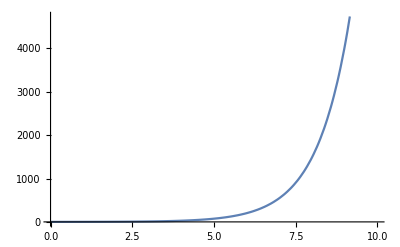

```mathematica
Plot[Sinh[x], {x, 0, 10}]
```

```mathematica
Limit[Sinh[x]/Exp[x], x->Infinity]
```

1/2

```mathematica
((Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep] ==Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep]))/.ep->λ/k1
```

Cosh[k1+2 r T λ-(2 r^2 T^2 λ^2)/k1]==Sinh[k1+2 r T λ-(2 r^2 T^2 λ^2)/k1]

```mathematica
Solve[((Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep] ==Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep]))/.ep->λ/k1, k1]
```

{}

```mathematica
Expand[%]
```

ⅇ^(λ/ep+O[ep]^2) O[ep]^1+ⅇ^(λ/ep+O[ep]^2) Cosh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^(3/2)] (x0+O[ep]^1)+ⅇ^(λ/ep+O[ep]^2) (-x0+O[ep]^1) Sinh[λ/ep+2 r T λ-2 (r^2 T^2 λ) ep+O[ep]^2]

```mathematica
Manipulate[Plot[{4 T^2 λ^2 σξ^2 (-1+Cosh[√x √(4 r T λ+x)]) a, (-2 T λ (T xh0 λ+(-r x0+xx0) x)+Cosh[√x √(4 r T λ+x)] (2 T^2 xh0 λ^2+2 T (r x0+xx0) λ x+x0 x^2)-√x √(4 r T λ+x) (2 T xx0 λ+x0 x) Sinh[√x √(4 r T λ+x)])},{x, 0, 10}], {T, 0, 5}, {x0, 0, 5}, {xh0, 0, 5}, {xx0, 0, 5}, {λ, 1, 1},{σξ,0,5}, {a, 0, 5}, {r, 1, 10}]
```

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[%126, {K1[tp]}, tp]
```

{(ⅇ^K1[tp] (8 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ^2 σξ^2 K1[tp] (4 r (T-tp) λ+K1[tp]) K1'[tp]-4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1[tp] (4 r λ-K1'[tp]) K1'[tp]+4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 (4 r (T-tp) λ+K1[tp]) K1'[tp]^2+8 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp]))) (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp] (K1[tp] (2 r λ-K1'[tp])+2 r (-T+tp) λ K1'[tp])-4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp] (K1[tp] (2 r λ-K1'[tp])+2 r (-T+tp) λ K1'[tp]+√K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp])-ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) K1[tp] (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)-ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (4 r (T-tp) λ+K1[tp]) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)-ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) √K1[tp] √(4 r (T-tp) λ+K1[tp]) (2 r (T-tp) λ+K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (2 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 K1[tp]+(1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])+2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1'[tp]^2)+1/2 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) √K1[tp] √(4 r (T-tp) λ+K1[tp]) (-(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^2+8 ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp]))) r (T-tp) λ σg^2 K1[tp] (2 r (T-tp) λ+K1[tp])+4 ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp])) σg^2 K1[tp]^2 (2 r (T-tp) λ+K1[tp])+4 (1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp) λ σg^2 √K1[tp] √(4 r (T-tp) λ+K1[tp])+4 (1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp])-4 ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp])) σg^2 K1[tp]^(3/2) (2 r (T-tp) λ+K1[tp]) √(4 r (T-tp) λ+K1[tp])-3 (-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) σg^2 K1[tp] (4 r (T-tp) λ+K1[tp])+8 ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp]))) (T-tp)^2 λ^2 σξ^2 (2 r (T-tp) λ+K1[tp]) K1'[tp]^2)-4 ⅇ^(-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp)^2 λ^2 σξ^2 K1[tp] (4 r (T-tp) λ+K1[tp]) K1''[tp]))/(2 K1[tp]^2 (4 r (T-tp) λ+K1[tp])^2)==0}

```mathematica
Simplify[%]
```

{(2 ⅇ^(K1[tp]-√K1[tp] √(4 r (T-tp) λ+K1[tp])) (T-tp) λ (2 ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) r σg^2 K1[tp]^3+4 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 r (T-tp)^2 λ^2 σξ^2 K1'[tp]^2-2 (-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) r (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) K1'[tp]^2+(-1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))) K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp]) (r (-1+2 r (T-tp) λ) σg^2+4 r (T-tp) λ^2 σξ^2 K1'[tp]+(-T+tp) λ σξ^2 K1'[tp]^2)-2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ σξ^2 K1[tp] (-4 r λ K1'[tp]+(-1+2 r (T-tp) λ) K1'[tp]^2+4 r (T-tp) λ K1''[tp])+K1[tp]^2 (r (1+ⅇ^(2 √K1[tp] √(4 r (T-tp) λ+K1[tp]))+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])) (-2+8 r (T-tp) λ)) σg^2+4 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 λ σξ^2 K1'[tp]-(-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ σξ^2 K1'[tp]^2-2 (-1+ⅇ^(√K1[tp] √(4 r (T-tp) λ+K1[tp])))^2 (T-tp) λ σξ^2 K1''[tp])))/(√K1[tp] (4 r (T-tp) λ+K1[tp]))==0}

```mathematica
FullSimplify[%129]
```

{(ⅇ^K1[tp] (T-tp) λ (r σg^2 K1[tp]^3+4 r (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])]) K1'[tp]^2-2 r (T-tp)^2 λ^2 σξ^2 √K1[tp] √(4 r (T-tp) λ+K1[tp]) Sinh[√K1[tp] √(4 r (T-tp) λ+K1[tp])] K1'[tp]^2+K1[tp]^(3/2) √(4 r (T-tp) λ+K1[tp]) Sinh[√K1[tp] √(4 r (T-tp) λ+K1[tp])] (r (-1+2 r (T-tp) λ) σg^2+(T-tp) λ σξ^2 (4 r λ-K1'[tp]) K1'[tp])-2 (T-tp) λ σξ^2 (-1+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])]) K1[tp] (-4 r λ K1'[tp]+(-1+2 r (T-tp) λ) K1'[tp]^2+4 r (T-tp) λ K1''[tp])+K1[tp]^2 (r σg^2 (-1+4 r (T-tp) λ+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])])+λ σξ^2 (-1+Cosh[√K1[tp] √(4 r (T-tp) λ+K1[tp])]) (K1'[tp] (4+(-T+tp) K1'[tp])+2 (-T+tp) K1''[tp]))))/(√K1[tp] (4 r (T-tp) λ+K1[tp]))==0}

```mathematica
%/.{K1[tp]->c*tp, K1'[tp]->c, K1''[tp]->0}
```

{1/(√(c tp) (c tp+4 r (T-tp) λ))ⅇ^(c tp) (T-tp) λ (c^3 r tp^3 σg^2+4 c^2 r (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])-2 c (T-tp) tp λ (-4 c r λ+c^2 (-1+2 r (T-tp) λ)) σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+c^2 tp^2 (c (4+c (-T+tp)) λ σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+r σg^2 (-1+4 r (T-tp) λ+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)]))-2 c^2 r (T-tp)^2 √(c tp) λ^2 √(c tp+4 r (T-tp) λ) σξ^2 Sinh[√(c tp) √(c tp+4 r (T-tp) λ)]+(c tp)^(3/2) √(c tp+4 r (T-tp) λ) (r (-1+2 r (T-tp) λ) σg^2+c (T-tp) λ (-c+4 r λ) σξ^2) Sinh[√(c tp) √(c tp+4 r (T-tp) λ)])==0}

```mathematica
Limit[1/(√(c tp) (c tp+4 r (T-tp) λ))ⅇ^(c tp) (T-tp) λ (c^3 r tp^3 σg^2+4 c^2 r (T-tp)^2 λ^2 σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])-2 c (T-tp) tp λ (-4 c r λ+c^2 (-1+2 r (T-tp) λ)) σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+c^2 tp^2 (c (4+c (-T+tp)) λ σξ^2 (-1+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)])+r σg^2 (-1+4 r (T-tp) λ+Cosh[√(c tp) √(c tp+4 r (T-tp) λ)]))-2 c^2 r (T-tp)^2 √(c tp) λ^2 √(c tp+4 r (T-tp) λ) σξ^2 Sinh[√(c tp) √(c tp+4 r (T-tp) λ)]+(c tp)^(3/2) √(c tp+4 r (T-tp) λ) (r (-1+2 r (T-tp) λ) σg^2+c (T-tp) λ (-c+4 r λ) σξ^2) Sinh[√(c tp) √(c tp+4 r (T-tp) λ)]), T->Infinity]
```

$Aborted

```mathematica
Limit[%134,T->Infinity]
```

{ConditionalExpression[False,(c^3 r tp^3 σg^2|σξ^2|σg^2)∈ℝ&&√(c tp)>0&&r λ>0]}

```mathematica
FullSimplify[%]
```

$Aborted